## Supplementary Materials for

Selection and gene flow shape genomic islands that control floral guides

Hugo Tavares, Annabel Whibley, David Field, Desmond Bradley, Matthew
Couchman, Lucy Copsey, Joane Elleouet, Monique Burrus, Christophe Andalo,
Miaomiao Li, Qun Li, Yongbiao Xue, Alexandra B. Rebocho, Nick Barton,
Enrico Coen

This PDF file includes:

	Materials and Methods
	Supplementary Text S1 to S5
	Supplementary References
	Figs. S1 to S16
	Tables S1 to S8

Note: This notebook contains “closed cells” that contain working and code for generating the figures. To see these, use “Cell:Cell properties: Open”.  Cells may also be grouped: double click at right to expand.

## Materials and Methods

#### Plant material

We studied a hybrid zone between two subspecies of Antirrhinum majus, A. m. pseudomajus and A. m. striatum, in the Spanish Pyrenees, near the village of Planoles, centred at latitude 42.322701, longitude 2.07442. For each plant, the following data were recorded: a global positioning system (GPS) coordinate (localised to within 2m using a Trimble GeoXT datalogger); a flower  colour score (as described in (1)); a photograph of a representative open flower; and leaf material (silica-dried for DNA extraction). Over a three-year period, a total of over 2000 individuals were sampled from populations from the centre to the flanks of the hybrid zone and were mapped onto a transect of 25km. Leaf material from six pools of ~50 individuals from populations along the transect were also collected for sequence analysis along with four pools of individuals from other A.m.pseudomajus and A.m.striatum populations sampled in the same manner (Table S1, Fig. S1).

Genetic crosses were performed in glasshouses, or on outside benches during summer, at the John Innes Centre as described in (2). Highly inbred stock lines used were A. majus stock JI7 and A. majus ros^dorsea(3). Stock lines of species accessions were established from A.m.pseudomajus individual J1428 (4.8 km east of hybrid zone centre; stock V164- 60) and A.m.striatum J1324 (13 km west of centre; stock V204-1).

#### A. majus reference genome

The draft reference genome (version 1.0) was constructed from the inbred A. majus JI7 stock line and consists of 87,577 scaffolds and contigs (http://bioinfo.sibs.ac.cn/am). We used only scaffolds and contigs >10kb in length in our analyses, corresponding to a total of 1592 scaffolds and ~480Mb genomic sequence. Of these, 1348 scaffolds, with a combined length of ~443Mb, have been placed into 8 linkage groups (corresponding to the 8 Antirrhinum chromosomes) using a mapping population of 48 recombinant inbred lines derived from an A. majus x A. charidemi cross. Analyses were conducted using a modified genome version in which a ~930kb superscaffold (ros_assembly) was constructed for the ROS1 region and replaced scaffold117, scaffold678 and C8923637.  This super-scaffold is available at https://github.com/JIC-Enrico-Coen/antirrhinum-ros-analysis. The constituent scaffolds are present entirely and are unmodified but were ordered, oriented and linked following the identification of coding sequences from known genes (ROS1 and ROS2) split across scaffolds. The components of the ros_assembly superscaffold are: scaffold 678 (position 1-543,204, forward orientation), C8923637 (543,205-550,832, forward orientation) and scaffold 117 (558,009-926,792, reverse orientation). An additional 7.2kb segment was introduced to link C8923637 to scaffold 117 following analysis of de novo assemblies generated with Velvet 1.2.03 (4) and ABySS 1.3.7 (5) from Illumina 100bp paired-end sequencing of a 200kb BAC clone containing the ROS1 gene from a library provided by Zsuzsanna Schwarz-Sommer (6).

#### DNA extraction

Genomic DNA was extracted from the pooled samples using a CTAB-based extraction method as described in (7). Individual DNA samples were extracted either using the DNeasy Plant Mini Kit or DNeasy 96 Plant Kit (Qiagen) following manufacturer's instructions or the method described in (8).

#### Re-sequence analysis

PoolSeq library properties are summarized in Table S2. Paired-end Illumina reads were quality-filtered using Trimmomatic (v.0.32; (9)) with the following settings: ILLUMINACLIP:TruSeq3-PE.fa:2:30:10 LEADING:3 TRAILING:3 SLIDINGWINDOW:4:20 MINLEN:50. The filtered fastq reads were mapped to the A. majus reference using stampy (v.1.0.28; (10)). All default settings were used except the setting of an explicit substitution rate to account for expected divergence from the reference (--substitutionrate 0.02). Mapping statistics are summarized in Table S3. Alignment file manipulations used SAMtools v1.3.0 (11). After mapping, duplicate reads were excluded using the MarkDuplicates tool in Picard (v1.134; http://broadinstitute.github.io/picard) and local indel realignment using IndelRealigner was performed with GATK(v3.5.0; (12)). For PoolSeq, sequence read alignments were converted to pileup format using SAMtools mpileup with a minimum mapping quality of 40, a minimum base quality of 30, the inclusion of orphaned reads (-A) and disabled probabilistic realignment for the computation of base alignment quality(-B). Popoolation2 (v1.201; (13)) was used to convert from pileup to sync format, the input required for population genomics analyses. Sites annotated as repeats in the reference genome were removed using bedtools (2.24.0; (14)). For fine-mapping of recombinant breakpoints the same process of read quality control and mapping was followed. Reference and variant bases were called using UnifiedGenotyper in GATK and recombination breakpoints were localized using custom scripts.

#### Population genomics

Population genomics analyses were done with a custom Python script (available at: https://github.com/dfield007/slidingWindows). We applied minimum and maximum coverage thresholds per site of 15 and 500 respectively and required that a site fall within these limits in all ten populations. To limit the impact of sequence errors, which can be conflated with low frequency alleles, the minor allele at a site had to be detected in at least two independent pools and in each case supported by a minimum of two reads.

We estimated diversity within-populations (π_w), diversity between (π_b = D_xy; absolute divergence), relative divergence between populations (F_st) and total diversity (π_t). For biallelic sites we let the allele frequencies be p_i and p_j in population i and j, respectively. Sites with n>2 nucleotides were rare; we removed the least frequent allele prior to calculations. We then calculate for each site and in each population, π_w = 2 p_i(1-p_i), and for each population pair, π_t= 2 p_ij(1-p_ij), where p_ij is the allele frequency for the two populations combined. The contribution of each population to the total is weighted following Charlesworth (15). We adjusted π_w and π_t to account for sampling errors due to pooled data following Futschik & Schlötterer (16). Here, we multiply diversity statistics by [(M-1)/(M-2b+1)], where M = depth, b = minimum read count for allele call. Similarly, we estimate for each population pair, π_b=p_i(1-p_j)+p_j(1-p_i). Window means are calculated for these measures, and then relative divergence estimated as F_st=(π_b-(π̄)_w)/(π_b+(π̄)_w) where (π̄)_w is the mean diversity within population i and j. In the analyses presented here, statistics were calculated as averages over 10kb windows with a  1kb step, with the exception of the whole genome profile shown in Fig.2A in which a 50kb window and 25kb step size was used. Windows in which the number of sites meeting quality thresholds constituted less than 10% of all sites were excluded.

#### Genotyping

Several methods for genotyping individuals were used: standard PCR; KASP technology (LGC Genomics); Sanger sequencing; multiplex PCR; cleaved amplified polymorphic sequences (CAPS). Primer sequences are shown in Table S4. Further details of genotyping screens are provided in Supplementary Text S3.

Standard PCR was used for genotyping indel polymorphisms that could be visualized on 1-2% (w/v) agarose gels. Annealing temperatures of 55°C were typically used. Sanger DNA sequencing was used to genotype SNPs and small indels from regions amplified by PCR. The amplified regions were between 500bp - 1kb. The sequencing PCR reaction was prepared using the BigDye Terminator v3.1 Cycle Sequencing Kit (Life Technologies), following the manufacturer' protocol. Identification of SNP and small indel polymorphisms was made using the Mutation Surveyor software (demo version 4.0).

KASP technology was used to genotype bi-allelic SNPs. The genotyping reaction was prepared according to the manufacturer' protocol (LGC Genomics). Reactions were performed either in 96-well or 384-well format, in 10 or 5μl volumes, respectively. After 30-40 PCR cycles, the fluorescence was read in a real-time PCR thermocycler (BioRad CFX96 or Roche LightCycler480).

Multiplex PCR was used to combine seven markers in a single genotyping reaction (markers 1, 2, 3, 7, 16, 32 and 38 in Table S4, with each primer at final concentration of 2μl). The markers were fluorescently tagged and analyzed by capillary electrophoresis. The PCR reaction was prepared using the Multiplex PCR Kit (Qiagen), following the manufacturer' protocol. Thermal cycling conditions were: 95°C for 3 min; 28 cycles at 95°C for 15 sec, 60°C for 1 min and 72°C for 45 sec; final extension at 60°C for 30 min. 1μl of the PCR product was mixed with 10μl Hi-Di Formamide (Applied Biosystems) and 0.1μl GeneScan-500 ROX size standard (Applied Biosystems). Genotypes were scored using the GeneMarker software (demo version 2.6.0).

The CAPS method was used to distinguish restriction polymorphism between alleles. A standard PCR reaction was performed as detailed above, followed by a restriction digestion reaction, using the enzymes SpeI (Roche) for marker 8 and MseI (Roche) for marker 11. 6μl of PCR product were digested in a 10μl reaction, following the manufacturer' protocol. The digestion reaction was performed at 37°C for 2h, after which it was analysed by electrophoresis in a 2% (w/v) agarose gel.

#### Geographic clines

To quantify the steepness of clines in allele frequencies and infer the presence of a barrier to gene flow, the KASP genotyping platform (LGC) was used to genotype SNP loci at Rosea and Eluta and ~1Mb of the surrounding chromosome. We genotyped 1722 individuals for a representative sample of SNP loci showing steep clines in allele frequencies (from PoolSeq) within domains of Rosea (ROS1, ROS2, ROS3) and Eluta (EL), in the intervening 0.5cM region between ROS and EL and both up and downstream of ROS and EL. As a control, seven of the 30 loci were polymorphic in the hybrid zone (0.3 < p < 0.7). These SNPs were also used to compare allele frequency estimates in the PoolSeq dataset with expected frequencies given by the genotypes of the individuals within two pools: YP4 and MP11. The correlation between KASP genotype frequency estimates and PoolSeq estimates for 30 SNPs is shown in Fig. S2. DNA extractions and genotyping were carried out by LGC Genomics. Plants were grouped into discrete demes of 200x200 metres, and their position collapsed along a 25km one-dimensional transect (Fig. S8). We fitted a five-parameter symmetric sigmoid cline to the observed data (centre, width, p_0, p_1, F_st) using maximum likelihood and a simulated annealing algorithm (iterations = 50,000, burn-in = 2000) with a custom R script. The most likely cline parameters and their 95% credible intervals were estimated for each SNP locus from three replicate runs, each beginning with randomly generated starting parameters (for more details see Supplementary Text S2).

#### RNAseq

RNAseq was used to investigate the gene expression in the flowers of individuals homozygous for different ROS-EL genotypes. The main purpose of this experiment was to aid in the identification of a candidate gene in the ~50kbp interval to where the EL locus was fine-mapped. Therefore, the genotypes analysed were chosen based on whether individuals carried a dominant or recessive allele at each locus, in different combinations. We also included individuals with a recombinant ROS1 allele (which gives a pale magenta phenotype, as exemplified in Fig. 1H) to relate the expression of ROS1 to their phenotype. The individuals used in these experiments are progeny from the mapping populations described in Supplementary Text S1. Therefore, the A. m. pseudomajus and A. m. striatum ROS-EL alleles assessed in this experiment no longer occur in their native genetic backgrounds, but rather in a mixed background resulting from backcrosses to the A. majus inbred stock lines JI7 (magenta) or rosea^dorsea. The genotypes assessed and their family ID number are: ROS^m el^m (A183), ROS^p el^p (A181), ROS^* el^p (A177), ROS^m EL^s (A172), ROS^p EL^s (A174), ros^s EL^s (A182), ros^dor el^dor (A181).

Plants from these mapping populations were grown together on outside benches and the corolla of a 5-10mm flower bud was collected from each and immediately placed on dry-ice, after which it was stored at -80°C until RNA extraction. The size of flower buds was chosen based the fact that ROS1 is highly expressed at this stage (3). We used three independent biological replicates for each of the 7 genotypes assessed, for a total of 21 samples. For RNA extraction, the tissue was disrupted using a TissueLyser (Qiagen) before extraction with the RNeasy Plant Mini Kit (Qiagen), following the manufacturer' protocol and including on-column DNase digestion. Samples were stored at -80°C until use. Illumina Truseq 50bp single-end libraries were prepared and sequenced at the Earlham Institute, Norwich.

For analysis, sequencing reads in fastq format were first quality filtered using the software cutadapt 1.16 (18) with the following non-default options: --trim-n --quality-cutoff 20 --minimum-length 30 --max-n 0. For all except three samples, >98% of reads were retained after this filtering step. For three samples only ~75% of reads were retained, which was due to a portion of the tiles in the sequencing flowcell producing low quality sequences, possibly due to damage. Despite this, these libraries had one of the highest number of total reads, and the number of retained high-quality reads was within the range of most samples (20 to 60 million reads; one sample, with a ros^dor el^dor genotype only had 1M reads). These high quality reads were used to quantify the expression of annotated transcripts with salmon 0.9.1 (31). Before differential expression analysis, we used the R/Bioconductor package tximport (32) to summarise the transcript quantifications at the gene-level. Differential expression analysis was done using the R/Bioconductor package DESeq2 (17), using those gene-level quantifications. The test design was set such that we could contrast the effects of dominant and recessive alleles for both ROS and EL. The first contrast (ROS vs ros) was used as a control to see if the ROS1 gene was identified as differentially expressed between samples carrying the two types of alleles. The second contrast (EL vs el) was used to find candidate genes within the ~50kb interval where we fine-mapped ELUTA. We also specifically looked at the test results for known genes that encode enzymes in the anthocyanin biosynthetic pathway. Sample clustering based on whole-transcriptome data revealed one of the samples as an outlier from the rest (Fig. S6A). Analyses were conducted with and without this outlier sample and the qualitative patterns reported in Fig. S6 are robust to the removal of this sample from the set, including the identification of the candidate ELMYB transcription factor. The dataset reported here excludes the outlier sample, although the normalized gene counts are included in Fig. S6C-F. All analysis code is available at https://github.com/JIC-Enrico-Coen/antirrhinum-ros-analysis.

## Supplementary Appendix

### Supplementary Text S1: Inference from pairwise diversity and divergence, π_w, π_b

#### S1.1: Explaining the F_stpeaks at ROS and EL

The most obvious explanation for the two regions of reduced diversity at ROS and EL is that they are due to the sweep to fixation of one or more favourable mutations. Each such selective sweep would reduce diversity over a map distance r~2/τ, where τ is the time from origin of the mutation to its fixation. More precisely, after a single strongly selected mutation sweeps from low frequency to fixation, each sampled genome carries a random section of the unique genome on which the mutation arose; the length of this section is approximately exponentially distributed on either side, with mean 1/τ (21). We use this simple approximation to estimate the duration of the sweep, τ, and to find confidence limits on this estimate. Our estimates of the reduced diversity at ROS and EL are based on a sample of 200 genomes (50 diploid individuals from two pools, 2.5Km apart on either side).  We therefore draw 200 pairs of exponentially distributed values, each with mean 1/τ, and find how the number of identical genomes decreases from 200, as we move away from the focal mutation. When this number falls to 200√(1/2)~141, the pairwise diversity, π, will have been reduced by 1/2.  Replicating 1000 times, we find that the map length within which π is reduced by at least 1/2 spans on average 2.43/τ, with standard deviation ±0.155/τ.

#### Confidence limits on sweep duration

My original estimate (below) was wrong, because it considered individual genomes, not the overall length of the region of reduced diversity.  It would be better to simulate n=100 genomes, each with an exponentially distributed length, and thus find the distribution of the # of founder haplotypes. Suppose that at some point p=k/n genomes are from the founder. Then, π^*=(1-p^2)π, and so diversity is reduced by 50% at the point where p=0.71.  Sampling 200 genomes, we find that this π^*/π~0.5 interval spans on average 2.43/τ, with sd 0.155/τ, so that the 95% interval is 2.12 to 2.74/τ.

```mathematica
tt=Sort[#]⟦141⟧&/@RandomReal[ExponentialDistribution[1],{1000,200}];
{2Mean[tt],√(2Variance[tt]),MinMax[tt]}
```

{2.43244,0.155214,{0.934486,1.57821}}

This yields an estimate of τ~1700 (1500-1950) for ROS and 5100 (4400,5700) for EL

```mathematica
{2.43,2.12,2.74}/#&/@{0.0014,0.00038}//TableForm
```

1735.71 | 1514.29 | 1957.14
6394.74 | 5578.95 | 7210.53

old estimates - wrong

```mathematica
{FindRoot[(1+a) ⅇ^-a ==0.025,{a,5}],FindRoot[1-(1+a) ⅇ^-a ==0.025,{a,0.1}]}
```

{{a→5.57164},{a→0.242209}}

The 2-unit support limits are {0.05, 4.50}, while the 95% confidence limits are {0.24, 5.57}. Note that the expected interval is 2/t, but the MLE is 1/t - just because the likelihood is very skewed.

```mathematica
tl= t/.FindRoot[-2==Log[t ⅇ^(1-t)],{t,#}]&/@{0.1,2}
```

{0.0524691,4.50524}

```mathematica
{{0.0525,2,4.505}/0.0014,{0.0525,2,4.505}/0.00038}//TableForm
```

37.5 | 1428.57 | 3217.86
138.158 | 5263.16 | 11855.3

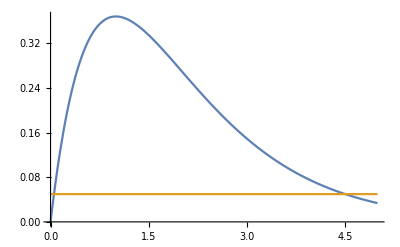

```mathematica
Plot[{t ⅇ^-t,ⅇ^-3},{t,0,5}]
```

```mathematica
{FindRoot[0.025==∫_0^x t ⅇ^-t ⅆt,{x,0.1}],FindRoot[0.025==∫_x^∞ t ⅇ^-t ⅆt,{x,0.1}]}
```

{{x→0.242209},{x→5.57164}}

Diversity is reduced by ~1/2 over ~45kb and ~12kb at ROS and EL, respectively (Table S7A). If the causal loci are placed at the centres of each peak, they are ~160kb apart, corresponding to the experimentally estimated recombination rate of 0.5cM for the ROS-EL interval, or 3.125 cM per Mb.  Hence, the reduction in diversity is over r~0.140 cM for ROS  and 0.038 cM for EL. This implies sweeps that had duration τ~2.43/0.0014 ~1700 generations for ROS and 2.43/0.00038~6400 generations for EL.  The distribution is approximately Gaussian, and so the 95% confidence intervals are ~(1500-1900) for ROS and ~(5600, 7200) for EL. These confidence intervals account for the randomness of evolution during the sweep, but do not allow for drift following the sweep, which will somewhat reduce the effective number of sampled genomes.

In a well-mixed population, τ~1/slog(4 N_e s), which would imply weak selection, s<0.001. However, spread across a spatially extended population takes much longer: an allele would take τ~(R/σ)/√(2s) generations to spread over a radius R, if genes diffuse at rate σ^2 per generation. Thus, narrow regions of reduced diversity are not inconsistent with strong selection - for example, a mutation with advantage s=0.2 would take ~1600 generations to spread over 1000σ dispersal ranges. Moreover, there may have been multiple overlapping sweeps, which will tend to broaden the region of reduced diversity.

Immediately after a ‘hard’ sweep, all diversity is eliminated close to the selected site. In fact, the average diversity has a minimum at π_w~0.0025 at ROS, and 0.0027 at EL (data from Fig. S9). After T generations, we expect that mutation at rate μ will generate π_w=2μT.  Assuming that μ=1.5×10^-8 per site per generation (22), this implies that very roughly, the most recent sweep occurred at T~83000 generations at ROS, and T~90000 at EL - or more recently, if soft sweeps had not eliminated all diversity. Most of the error in these estimates come from the evolutionary process, as simulated in Fig. S13 (top, Nm=0) ; there, the standard deviation of π_w, relative to the mean, accounting for both random initial SNP frequencies and variation between simulations, is 0.324. Therefore, the 95% confidence intervals are roughly (29 000, 137 000) for ROS, and (32 000, 148 000) for EL.  Note that most variance comes from the evolutionary process, rather than from sampling error in estimating the actual π_w in the population, which is much smaller.

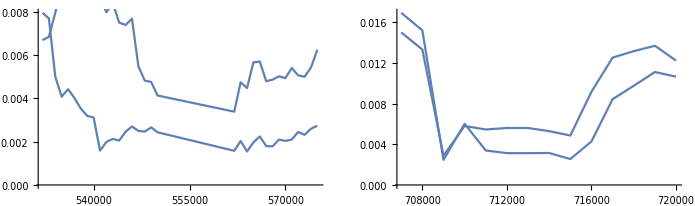

{0.00248066,0.00267451}

83333.3 | 29333.3 | 137333.
90000. | 31680. | 148320.

```mathematica
Show[GraphicsRow[Show[ListLinePlot[st[{4,5}][#]⟦All,{1,2}⟧],ListLinePlot[st[{4,5}][#]⟦All,{1,3}⟧]]&/@{{"ROS1 A","ROS1 B"},"EL"}]]
Min[st[{4,5}][#]⟦All,{2,3}⟧.{1/2,1/2}]&/@{{"ROS1 A","ROS1 B"},"EL"}
```

#### Reconstructing the s.d. in π_w

This reads in the simulation data used for the distribution of F_st

```mathematica
SetDirectory["/Manuscripts/RosEl April 2017/Antirrhinum - genomic clines/Antirrhinum_genomeData"];
```

```mathematica
<<"piRepsNew s[0], s[0.1], s[6.4] R=5 mu=2.7 2N=200";
```

This sets up functions that process  100 throws of 17 windows onto each of 10 simulations. mnt[Nm,f[{π_b,π_w}] return the mean π_w for each simulation, and sdt[] the mean standard deviation across throws.

```mathematica
?piReps
```

piReps[𝒫,i,t,j,n_w,n_reps] makes n_reps replicate throws of n_w windows from simulation 𝒫 at time t, using data from pSNP⟦All,j⟧. The dummy index i allows one to store results from different simulations. Requires allwindows, refWindows, tp and uses demes {1;;100,101;;200}

```mathematica
mnt[m_,f_]:=Table[Mean[Flatten[Map[f,piReps[s[m],k,40,4,17,100],{2}]]],{k,10}];sdt[m_,f_]:=Table[StandardDeviation[Flatten[Map[f,piReps[s[m],k,40,4,17,100],{2}]]],{k,10}];
```

This is the mean π_w for 2Nm=0, 6.4

```mathematica
Mean[mnt[#,#⟦2⟧&]]&/@{0,6.4}
```

{0.008647,0.0094505}

This is the mean sd between throws:

```mathematica
√(Mean[sdt[#,#⟦2⟧&]^2]&/@{0,6.4})
```

{0.00278506,0.00305302}

This is the mean sd between simulations:

```mathematica
StandardDeviation[mnt[#,#⟦2⟧&]]&/@{0,6.4}
```

{0.000226339,0.000121941}

This is the net sd including both sources:

```mathematica
√({0.002785,0.003053}^2+{0.00022634,0.00012194}^2)
```

{0.00279418,0.00305543}

π_w~0.0025, 0.0027 at ROS and EL, and ~2μt. setting μ=1.5 10^-8

```mathematica
{0.0025,0.0027}/(2 1.5 10^-8)
```

{83333.3,90000.}

```mathematica
0.00279/0.0086
```

0.324419

```mathematica
({1,1-2 0.324, 1+2 0.324}#/(2 1.5 10^-8))&/@{0.0025,0.0027}//TableForm
```

83333.3 | 29333.3 | 137333.
90000. | 31680. | 148320.

#### S1.2: The effects of a strong barrier to gene flow

We assume that a single ancestral population split into two at time T in the past; each of these populations has the same size, N_e, and the ancestral population is assumed to have been of size θ N_e. The diverging populations exchange M=N_e m individuals per generation.   Section S5.1 gives formulae for F_st as a function of T, M  and θ. Assuming that M~0 between ROS and EL (as implied by selection on two tightly linked loci; S5.2, S5.3), F_st would initially increase linearly with time, independent of θ, as F_st~t/(4 N_e). Thus, the observed F_st~ 0.125 would build up in t=0.5 N_e generations; the exact solution, with relative size of the ancestral population θ=2, is 0.54 N_e (S5.1). Outside the barrier, F_st quickly reaches an equilibrium between gene flow and drift, such that  F_st= 1/(1+16 N_e m); the observed F_st~ 0.019 for populations near the hybrid zone is consistent with exchange of N_e m=3.2 individuals per generation for these populations. (This should be regarded as an "effective number", since the actual relation depends on the detailed population structure).   We can estimate N_e from the diversity outside the ROS/EL region, π_w~0.010 (Table S7), which is expected to equal 8 N_e μ for a well-mixed ancestral population of θ N_e diploid individuals, with θ=2. (Since N_e m is large, diversity is hardly affected by the population split). Assuming μ=1.5×10^-8 as before, then N_e~83 000, and so T~0.54 N_e~45000 generations.  This is of the same order as the estimated time since the selective sweeps, 83-90 000 generations, which were made independently, from the residual diversity below the twin peaks. However, the data are also consistent with secondary contact between divergent populations, with F_st<0.12, at some time correspondingly more recent than 45 000 generations; such a scenario is illustrated in Fig. 6. Because F_st outside the ROS/EL region equilibrates quickly, these scenarios of primary vs. secondary contact cannot be distinguished (Fig. S14).

#### S1.3: Using simulations to test the significance of the F_st peaks

We simplify by comparing a complete barrier with gene flow N_e m=3.2, rather than modelling selected loci at ROS and EL explicitly. (It is not clear how one would do this, since selection would scale to unreasonably high values - see below).  Thus, we do not model the variation in divergence due to changes in barrier strength along the genome.  However, in S5.4, we do calculate the expected coalescence times along the genome.

It is not feasible to directly simulate structured populations with N_e~83000, over times of the same order.  Therefore, we follow (25) by scaling the simulations by a factor 830, running smaller populations for a shorter time. We simulate two populations, each with N_e=100 diploid individuals, for up to 100 generations. The populations either exchange genes at a rate N_e m=3.2, or evolve separately.  There are 5 crossovers per generation, which corresponds to a recombination rate in Antirrhinum of 5/830 = 0.0060, close to the observed recombination rate of 0.5cM, and equivalent to 193kb, or approximately 19×10kb windows.  The simulated mutation rate is 2.7 mutations per genome, which corresponds to μ=2.7/(830 193000) ≈ 1.7*10^-8 per site per generation. SNP frequencies are analysed exactly as for the real data, with the number of SNP being the same as in the actual data, based on random 10kb windows, randomly drawn from the 380kb flanking region.

Outside the ROS-EL region, the joint distribution of π_w, π_b in simulations is similar to that in the data, though somewhat less variable (compare Figs. 3, S11, and also Fig. 6, D, I with E, J). However, between ROS and EL,  F_st is far more variable than in simulations, and the various F_st peaks lie well outside the simulated distribution, assuming divergence across a complete barrier (Fig. S11).  Since variation in π_w,π_b is strongly correlated, and since the wide variation in π_w, π_b is anyway taken as given from the data, we now focus on the distribution of F_st.  With gene flow, this quickly reaches an equilibrium (Fig. S12, right), at the predicted value.  With no gene flow (Fig. S12, left), F_st increases through time; the best fit to the observed F_st = 0.125 is t=0.464 N_e, with 95% confidence interval 0.428-0.500 N_e, using a t-test based on the variation between replicates. Using the estimate of N_e=83 000 derived above, this corresponds to 38 500 (35 500, 41 500) generations - somewhat lower than the simpler “back of envelope” approximation used in the previous section. If there were initially a secondary contact between diverged populations, with F_st=0.05, then this would increase across the barrier (red dashed line at left), and decrease rapidly with no barrier (upper dashed red line at right).

We next examine the distribution of F_st, in order to find whether the various peaks are significant, relative to the null model of divergence across a strong barrier.   Given our simulation method, we can distinguish variance in F_st that is due to random assignment of SNP from that due to the underlying variation in ancestry. Variance due to SNP assignment is estimated from the variance within each replicate simulation (using 100 random assignments to the ancestral genomes of the same set of SNPs). Variance due to ancestry is estimated from the variance between replicate simulations. Figure S13 shows that with the density of SNP in the actual data (57167 in 930kb), the variance in F_st is about equally due to random variation in SNP frequency, and to variation in the underlying ancestry. The standard deviation of F_st in simulations with a complete barrier (Nm=0) is 0.0185, and the observed F_st in the ROS, middle and EL peaks was 0.391, 0.341, 0.243 respectively, compared with the mean in the intervening region of 0.125. This corresponds to 14.4, 11.7, and 6.4 standard deviations - all highly significant.

```mathematica
{√(0.0129^2+0.0133^2),(0.125-{0.391,0.341,0.243})/√(0.0129^2+0.0133^2)}
```

{0.0185284,{-14.3564,-11.6578,-6.36862}}

#### S1.4: Interpreting fluctuations in F_st

As well as the striking and consistent peaks in F_st at ROS and EL, there are other sharp features across this region: a “middle” F_st peak between ROS and EL; a ~5kb region of reduced diversity and divergence in the middle of the ROS peak; regions in which diversity is lower on one side, but π_b~π_w on the other, and other smaller features (Fig. S10). These features may appear only in some comparisons; for example, the “middle peak” does not appear in distant comparisons (Fig. 2B), but does with the other two pairs of pools (Fig. 2D, H).  Such heterogeneity could have a variety of causes. If a mutation sweeps across both hybridising populations, it would decrease both diversity and divergence (24), and give a dip in F_st. If a mutation sweeps through only one population, it will reduce diversity on only one side, giving a smaller F_st peak. If a block of genome introgresses from a divergent population or species, and sweeps to fixation within one of the two hybridising populations, it would generate an F_st peak with increased divergence, rather than reduced diversity.  Comparisons between different pairs of samples may give different patterns if divergence occurs at different places; in particular, we know that there is substantial divergence across the pass at the head of the Planoles valley (F_st = 0.035 between pools YP2, YP4, both in the regions flanking ROS and EL, and in-between them; these pools are 11Km apart). Once a strong barrier to gene flow is established, sweeps in that region (which may or may not be related to flower colour) will tend to be trapped, so that sharp features will accumulate there (29).  It may be possible to distinguish these possibilities by sampling individual haplotypes from a broad range.

The aim of this section has been to show that sharp rises or drops in F_st cannot be explained purely by a strong barrier to gene flow across the whole ROS/EL region - though sweeps may accumulate at such a barrier, leading to sharp F_st peaks (29). Our simulations show that these various sharp peaks in F_st are significant, relative to the overall broad increase in F_st that is generated by a strong barrier.

#### S1.5: Simulating the effects of selective sweeps and of a barrier to gene flow

Figure 6 illustrates a scenario in which divergence occurs in allopatry, due to random drift and selective sweeps; following secondary contact, divergence is eroded across the genome, except between two selected loci, which maintain a strong barrier to gene flow.  Initially, just after two populations are separated by a geographic barrier, F_st looks homogeneous (Fig. 6A). Two sweeps then occur, one on one side at ROS, the other on the other side, at EL (Fig. 6B). These reduce diversity in one or other population, leading to two sharp F_st peaks. Sweeps are simulated as regions that trace back to a single ancestral genome; breakpoints are exponentially distributed with mean 0.14 at ROS, and 0.1 at EL. Since simulations are scaled by a factor 830, these correspond to a time to fixation, τ, of 5930, 8300 generations, respectively.  SNP positions and frequency are drawn from pool YP1, as for the simulations used for inference.  The second row represents the population after a period of allopatric divergence. SNP frequencies are drawn from pools YP4, MP11, for which F_st~0.05 outside ROS-EL, corresponding to ~0.2 N_e generation (Fig. 6C). Two further sweeps have occurred at ROS and EL, simulated in the same way as before, leading to reduced diversity on both sides, and thereby strengthening the F_st peaks. Now, the populations come back into contact, and exchange genes at a rate N_e m=3.2 per generation - except in the ROS-EL region, where there is a complete barrier (Fig. 6D).  After a further 0.3 N_e generations, F_st outside ROS-EL has equilibrated, whereas F_st between ROS and EL has continued to increase. This period of secondary contact is simulated by starting with the allopatric divergence represented in Fig. 6C, and then simulating two populations with or without gene flow (to account for regions outside or in the ROS-EL region, respectively).

This scenario of secondary contact is distinct from the primary contact assumed in the simulations used for inference. However, they lead to essentially the same outcome, since gene flow outside the ROS-EL region leads to rapid equilibration. Note that the observed pattern of π_b, π_w, and hence of F_st in the ROS-EL region is much more heterogeneous than in simulations. This reflects the significant sharp features seen through this region, which include the sharp peaks at ROS and EL.

The data shown in Fig. 6E, and Table S7, were filtered in the same way as in Materials and methods: population genomics; informative sites were required to have coverage between 15 and 500, and windows were required to have at least 10% of sites within this range.

#### S1.6: Significance of clustering

Adaptive alleles can resist gene flow more effectively if they are linked.  Thus, if the selected loci responsible for divergence are seen to be clustered on the genetic map, or involved with chromosomal rearrangements that suppress recombination, this suggests that divergence occurred despite gene flow (30).  However, while there are good examples where chromosome rearrangements are associated with selected divergence, evidence for clustering is otherwise unclear (22).  In the hybrid zone between Antirrhinum majus striatum and A. m. pseudomajus, ROS and EL are closely linked.  Is this significant evidence for clustering?  Specifically, what is the probability that the closest pair of k loci are closer than ϵ apart?

Assume that k loci fall uniformly on a map of length R.  Then, the gaps between them are distributed exponentially with rate k/R, .  What is the probability that the (k-1) gaps are all greater than ϵ?  The chance that one gap is larger than ϵ is exp[-kϵ/R], and so the chance that (k-1) are all larger is exp[-k(k-1) ϵ/R] (Table S8). (This argument assumes independence, which is not quite exact, but simulations show that it is very accurate).

Assuming a genetic map of length 5.88 Morgans, the probability that the closest pair are closer than 0.5cM is 1.7% with 5 loci in total, and 7.4% with 10 loci.  We know that at least three loci influence flower colour (ROS/EL/SULF), and have preliminary evidence for at least two more.  Thus, finding this close a linkage is unlikely, and indeed, formally significant.  However, clustering of functional loci on the genetic map (e.g. due to tandem duplication of MYB transcription factors), and variation in recombination rate, would increase this probability. Thus, we regard this linkage as suggestive, but by no means definitive.

It is hard to see how clustering could have been selected for as a result of gene flow in Antirrhinum, which has an extensive geographic  range.  Suppose that one allele becomes established over a broad area, and gives a new floral phenotype that is maintained by some kind of selection.  Further alleles may improve its attractiveness to pollinators, and will be favoured wherever the first allele is sufficiently frequent.  Linkage will aid the establishment of such an allele only where populations are mixed (i.e., in hybrid zones). Yet, such zones are narrow relative to the species’ range, and indeed, we have only found a few of them.  Thus, it is hard to see that they can contribute significantly to clustering.

Alternatively, one could imagine that pairs of alleles are required to establish a new phenotype within a spatially structured population. The probability that these will be established can be greatly enhanced by linkage, because such events are extremely rare when neighbourhood size is large (27).   However, this also makes such a mode of establishment highly improbable: it is more likely that alleles are established one at a time, in which case gene flow has no effect.

### Supplementary Text S2: Geographic clines

To assess geographic clines in allele frequency at the Rosea and Eluta genes, 32 SNP markers were designed using the A. majus reference genome and hybrid zone PoolSeq dataset (see main text). We identified divergent SNPs on the basis of strong allele frequency differences (>0.6), in the outermost hybrid zone pools (YP4, MP11). We selected divergent SNPs associated with the genes in the ROS locus (ROS1, ROS2, ROS3) and with Eluta (EL), as well as in the intervening 0.5cM region and both up and downstream of ROS and EL (Table S5). As a control, seven of the 30 loci were selected on the basis of being polymorphic in the hybrid zone (0.3 < p < 0.7). All candidate SNP loci were filtered using a custom script SNPextract.py (https://github.com/dfield007/genomics_general) which identified SNP positions suitable for the KASP genotyping platform (LGC Genomics) and extracted the 100bp sequence surrounding each candidate SNP. The script was run with the following parameters: (i) 30 < depth < 300 in both outer pools at the focal SNP (to reduce the probability of false positives and paralogs), (ii) 30 < depth < 300 for sequences 50bp upstream and downstream of focal SNP, (iii) <3 other SNPs within 50bp (to ensure primer efficiency), and (iv) biallelism (a KASP requirement). DNA extractions and KASP SNP genotyping were carried out by LGC Genomics. Replicate DNA extractions and genotyping of n = 128 individuals confirmed relatively low error rates of the KASP platform (mean error rate <0.1%).

The hybrid zone lends itself to one-dimensional cline fitting due to the narrowness of the habitat along a primarily East – West valley with high mountains to the north and south that are above the altitude limit of these species. Antirrhinum plants are primarily found within 100m either side of two roughly parallel roads that run up the valley. First, allele frequencies and genotype counts were determined by dividing the area into a grid of 200 x 200 metre demes. This scale minimised deficits from Hardy-Weinberg equilibrium whilst ensuring sufficient sample size within demes (mean = 40, s.d. = 20, range 10-200). Only one marker within ROS1 displayed significant departures from HW with a deficit of heterozygotes (F>0) even at small spatial scales (50 metres). Theory predicts that F>0 can generate narrower cline widths than expected (19). However, here we are not directly testing for significant differences in steepness between individual SNP markers. To collapse the data to one-dimension, we fitted a transect through the approximate cline centre (p = 0.5 isocline) and examined cline width with a range of compass headings through the valley. We found that a heading of 300° generated the highest likelihood (log(L)) and the narrowest cline width (Fig. S8).

We fitted a five parameter, symmetric sigmoid cline to the observed genotype counts with the expected allele frequencies p̂ along the one-dimensional transect as:

p̂ = p_0+(p_1-p_0)/(1+exp[-4(x-c)/w])

where x = spatial coordinates in metres along the transect, c = cline centre, w = cline width (1/gradient), p_0 = allele frequency at the asymptote in the west (A.m. striatum parental allele frequency) and p_1 = allele frequency at the asymptote in the east (A.m. pseudomajus parental allele frequency). In addition, we fitted a beta-binomial error term to account for the variance in allele frequencies across demes and to control for population structure along the cline F_st= var(p)/p̄(1-p̄).

To fit clines to the data, we used a Metropolis-Hastings (simulated annealing) algorithm to sample the likelihood surface following (20) with a few modifications. Briefly, we begin with a random set of parameters which are changed randomly and the log likelihood log(L) is computed at each iteration. When the next iteration log(L)'' has a greater log likelihood than the previous likelihood log(L)', the new parameters are accepted. If the next iteration is lower (log(L)'' < log(L)'), we accept with a probability log(L)''/log(L)'. To ensure ample exploration of the likelihood surface, the jump size for the next set of parameters are adjusted by a factor of 1.05 when accepted (accept scale) and by (1/1.05) when parameters are rejected (reject scale). After some tests of different accept and rejection scales, we found these values achieved efficient mixing and exploration of the likelihood surface with an acceptance rate ~0.5. This algorithm was run for 50,000 iterations with a burn-in = 2000. From this we find the best fitting combination of parameters from the maximum log likelihood. To find the 95% credible intervals (95% CI) we assumed the likelihood surface follows a chi-square distribution. For each locus, we visually inspected the likelihood surface to ensure they were well mixed for each parameter. The algorithm was run on each locus three times with randomly chosen starting parameters to ensure that independent runs displayed similar parameter estimates with overlapping 95% CI.

Cline fitting identified steep clines with similar widths and centres for SNP loci located in the ROS and EL genes (Fig S3; ROS markers 7, 8, 10, 11 and 12; EL markers 20 and 21). For neutral SNP loci in the intervening region between ROS and EL that display strong allele frequency differences, these also exhibited geographic clines similarly steep to both ROS and EL (Fig S3; markers 14, 15, 16, 17, 18, 20). This is consistent with the presence of a barrier to gene flow due to the presence of two tightly linked genes under selection. In contrast, SNP loci situated upstream of ROS or downstream of EL showed shallower clines, a pattern expected for neutral loci which should homogenize through ongoing gene flow across the hybrid zone.

### Supplementary Text S3: Genotyping Screens

To dissect regions conferring flower colour phenotypes, we analysed recombinants around the ROS region in segregating populations. Two main approaches were taken: (1) blanket genotyping irrespective of phenotype, or (2) screening for recombinant phenotypes, followed by genotyping. The first approach allowed recombinants upstream and downstream of ROS and EL to be recovered. The second approach specifically targeted breakpoints falling between ROS and EL. A selection of 16 recombinant haplotypes obtained from this analysis were subject to whole genome sequencing to map breakpoints more precisely.

#### Blanket genotyping

One F2 population was derived from A.m.pseudomajus (ROS^p el^p) crossed to A.m.striatum (ros^s EL^s). 161 F2 plants were genotyped using markers 5 and 6 (Table S4). One recombinant was found carrying ROS^p EL^s. A second population was derived from A.majus (ROS^m el^m) crossed to A.m.striatum. We genotyped 685 F2 individuals with 4 markers (extending from ~75kb upstream of ROS1 to ~323kb downstream). 25 recombinants were identified and fine-mapped with 13 further markers from the ROS region (Fig3 B-F). Genotypes were determined by test-crosses to A.majus J7 (ROS^m el^m) or A.majus ros^dorsea (ros^dor el^m).

#### Targeted recombination analysis

A.m.striatum was crossed to A.m.pseudomajus or A.majus JI7. F1 plants (ROS el/ros^s EL^s) were test-crosssed to A.majus ros^dor el^m. This yielded mainly magenta (ROS el/ ros^dor el^m) or rosea phenotypes (ros^s EL^s/ ros^dor el^m) in the next generation. However, recombinants with genotype (ROS EL^s/ ros^dor el^m) gave Eluta phenotypes and could thus be easily distinguished. From 10,261 individuals screened over 3 years, 35 individuals had an Eluta phenotype. Genotyping showed that 10 of the Eluta plants had duplicated copies of ROS EL, suggesting possible chromosomal rearrangements, while 25 had a recombinant genotype of ROS EL^s. Four plants with a pale magenta phenotype were also recovered from the targeted recombinant screen (Fig.3I), along with a single individual with a similar phenotype from the blanket genotyping (Fig. 3C).

#### Analysis of ROS-EL haplotypes in the hybrid zone

ROS-EL haplotypes in the hybrid zone were determined from four molecular markers, two in ROS1 (markers 5 and 6; Table S4) and two in EL-MYB (markers 33 and 34; Table S4). These markers produced combinations of alleles that distinguished the two subspecies. Individuals heterozygous for both genes were considered to carry two parental haplotypes. We genotyped 2393 randomly sampled individuals, of which 4089 haplotypes were determined to be A. m. pseudomajus (n=2045), A. m. striatum (n=1843) or recombinant (134 ROS^p EL^s and 67 ros^s el^p). Individuals with discrepancies between the two linked markers for each gene and/or suspected genotyping errors were excluded from the analysis.

#### Progeny testing

In the 2012 field season, we selectively genotyped 187 individuals with rare phenotypes in the flanks, which allowed us to identify a further 33 recombinant haplotypes (30 ROS^e EL^s and 3 ros^s el^p). To genetically validate that these recombinant haplotypes conferred altered phenotypes (according to the expectations in Fig. 1), we test-crossed progeny from capsules collected from wild plants carrying those haplotypes. This was done to confirm that these putative recombinants were not due to a technical artifact, such as allelic dropout in our molecular markers (leading to mis-classifying an allele as the wrong subspecies). The progeny from 27 wild capsules of individuals carrying putative recombinant haplotypes were genotyped for ROS1 and EL-MYB, to identify which individuals carried the recombinant haplotype (in all cases these were heterozygous with a non-recombinant haplotype). These individuals were then test-crossed to a magenta A. majus inbred line (ROS^m el^m) and to the non-magenta inbred A. majus rosea^dorsea (genotype ros^dor el^m). Some of these crosses were also progeny tested to identify homozygotes. 47 haplotypes from the wild population were analysed in this manner.

In the progeny-testing we found that 4 out of 26 ROS^p EL^s/ros^s EL^s individuals and 2 out of 4 ROS^p EL^s/ROS^p EL^s individuals, were falsely determined to carry a ROS^p EL^s haplotype, due to a null A. m. pseudomajus EL-MYB PCR allele (they were in fact ROS^p el^p/ros^s EL^s and ROS^p el^p/ROS^p EL^s, respectively). Thus, our estimates of this type of recombinant haplotype (ROS^p EL^s) might be slightly overestimated in the hybrid zone. Despite this genotyping error, we genetically confirmed 16 ROS^p el^p (pseudomajus-like), 12 ros^s EL^s (striatum-like), 4 ros^s el^p and 15 ROS^p EL^s haplotypes. The parental haplotypes produced magenta (ROS^p el^p) and non-magenta (ros^s EL^s) flowers when homozygous. In the magenta phenotype, venation is cryptic, and so we did not consider its patterning; however, in the non-magenta phenotype, venation is obvious and in ros^s EL^s/ ros^s EL^s homozygotes the veins were restricted to the region where the two dorsal petals meet. In ros^s el^p/ros^s el^p recombinants the veins become spread across the dorsal petals and there is some pigment in the outer region of the petal lobes. In ROS^p EL^s haplotypes, flowers have an Eluta pattern. This indicates that our molecular screening of recombinants was effective at finding true recombinant haplotypes, despite the errors due to null alleles.

### Supplementary Text S4: Increase of recombinants in the hybrid zone

In this section, we consider the increase of recombinants between ROS and EL within the hybrid zone, which sets a lower bound on the age of this hybrid zone: the hybrid zone must have persisted for long enough for recombinants to build up to the observed frequency of ~10% at the centre (assuming an initially sharp contact between non-recombinant genotypes).  Since the two loci are r=0.5cM apart, heterozygotes generate 0.5% recombinant gametes.  At the centre of the hybrid zone, recombinants would increase at a rate 2rpq(1-F_is)=0.0025(1-F_is) per generation; F_is is the deficit of heterozygotes at ROS and EL. Thus, even disregarding the (slight) reduction in heterozygotes below Hardy-Weinberg, it would take at least 40 generations for recombinants to reach 10%.  However, this argument ignores spatial structure, which we now consider.

Suppose that the distinct populations met in a sharp step, and that selection rapidly established a sharp and stable cline between ROS/el and ros/EL haplotypes.  With selection s against heterozygotes, or linear frequency-dependent selection of strength s against rarer alleles, the cline between the parental haplotypes will have the form p=1/(1+exp[-4x/w]), where the cline width is w=√(8σ^2/s).  Recombinants would be produced at a steady rate 2rpq(1-F_is) within this cline, and in the absence of selection, would diffuse outwards at a rate σ^2, the dispersal rate.  This outward diffusion from a limited region will reduce the frequency at the centre, relative to the panmictic case just considered. After t generations, the frequency at the centre would be:

u_max=r/s(1-F_is)∫_0^st ∫_(-∞)^∞ exp[-X^2/τ]/(√(2π τ))2pq ⅆXⅆτ

where X=4x/w.  We could not find an analytic solution, but it can readily be evaluated numerically, and has the form (r/s)f[st]. If we take s=0.2, then recombinants would reach 10% at the centre by 85/(1-F_is) generations, whilst if s=0.1, this would take 61/(1-F_is) generations - a somewhat shorter time, because recombinants are being generated over a wider area.  Thus, assuming that the effective selection between the parental haplotypes is not extremely strong (i.e. s<0.2), and the contact less than 85 generations old, the observed frequency is consistent with neutral diffusion of recombinants. If the contact is older than this, then selection must act to restrain the increase of recombinants.

In principle, the spatial distribution of recombinants reflects the detailed nature of selection. for example, if one recombinant is fitter than the other, then the clines would be staggered such that that recombinant becomes commoner. However, there are a limited number of individuals in the hybrid zone, and so random drift obscures such patterns.

### Supplementary Text S5: Effect of a barrier to gene flow on divergence

In this section, we gather theoretical results on the change in diversity, divergence, and F_st through time, in the presence of barriers to gene flow between two demes, and in one dimension.  Specifically, we give formulae for:
	5.1) the increase in pairwise coalescence times within and between two demes connected by gene flow;
	5.2, 5.3) the strength of the barrier to gene flow due to two linked loci, between two demes, and across a one-dimensional cline;
	5.4) the effect of a barrier to gene flow in one dimension, compared with a barrier to flow between two demes. 
These theoretical results are needed to support arguments and parameter estimates that are made in the preceding sections (S1).

#### S5.1: Change in F_stover time

Suppose that a single well-mixed population, of effective size θN_e splits into two populations, each of size N_e, that exchange migrants symmetrically at rate m. We scale time and migration relative to 2 N_e, so that T=t/(2 N_e), M=2 N_e m.  For two populations, F_st=(T_b-T_w)/(T_b+T_w) is defined in terms of the mean coalescence times for two genes from within a population, or between two populations. These coalescence times are given by (23):

∂_T T_w=1+2M(T_b-T_w)-T_w
∂_T T_b=1+2M(T_w-T_b)

Initially, T_w=θ, and T_b=T_w((1+F_0)/(1-F_0)). The terms correspond to the passage of time, migration, and (for T_w only) coalescence. From (23), the solution is:

T_w=2+ⅇ^(-1/2 T (1+4 M)) ( (θ-2)Cosh[(γ T)/2]+1/γ Sinh[(γ T)/2] (4 M (θ((1+F_0)/(1-F_0))-2)-θ))  
T_b=(1+4 M)/(2 M)-1/(2  M)ⅇ^(-1/2 (1+4 M) T) ( ( (1+4 M)-2 ((1+F_0)/(1-F_0)) M θ) Cosh[(γ T)/2 ]+ 1/(2γ)Sinh[(γ T)/2]( (8 M+θ-γ^2( θ-2))-4 ((1+F_0)/(1-F_0)) M θ))
where γ=√(1+16 M^2).

These results are compared with simulations in Fig. S12, and to estimate T, M=N_e m in section S1.2.

#### S5.2: Barrier to gene flow due to two linked loci: one deme

In this section, and the following one, we show that two linked loci cause a strong reduction in the rate of gene flow in the region between them, which justifies our use of simulations with no gene flow in section S1.

Selection on linked loci reduces the effective rate of immigration by a factor that depends on the relative rates of recombination and selection. Barton and Bengtsson (26, Eq. A6) give a general recursion for the reduction in the effective rate of gene flow, for an arbitrary number of selected loci, assuming weak selection and recombination, and a low rate of flow into each deme, so that only the marginal (additive) effects of sets of alleles need be considered.  Multiple crossovers are ignored in this continuous-time limit..

A single selected locus, with selective disadvantage s>>m in the focal population, will reach equilibrium frequency m/s. The effective rate of influx of neutral alleles is then reduced to:

m_eff/m = r/(s+r)

For two loci, under selection s_1, s_2, with no epistasis, and a neutral locus in-between:

m_eff/m = r_1/(s_1+r_1)r_2/(s_2+r_2)

This is just the product of effects of each locus separately.  For a neutral locus to the left of selected locus 1, recombining at rates r_1, r_2=r_1+r_(1,2) with the two selected loci:

m_eff/m = r_1/(s_1+r_1)(r_2+s_1)/(s_1+s_2+r_2)

This is the product of the effects of the two loci, but with the recombination rate with the second locus, r_2, replaced by r_2+s_1. Thus, the effect of the second locus on gene flow is reduced by an increase in the effective recombination rate.  When selection is strong relative to recombination, this greatly weakens the effect of the barrier outside the two loci, relative to that between them.

The effect of the reduction in effective rate of gene flow on coalescence times and on F_st can be found by rescaling M=2 N_e m in the previous section.

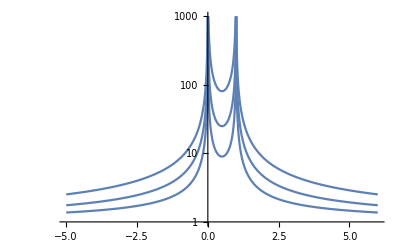

```mathematica
ss={4,2,1};LogPlot[1/If[x<0,(-x)/(ss+(-x))(1-x+ss)/(2ss+1-x),If[x>1,(x+ss)/(2ss+x)(x-1)/(ss+x-1),x/(ss+x)(1-x)/(ss+(1-x))]],{x,-5,6},PlotRange->{{-5,6},{1,1000}}]
```

#### S5.3: Barrier to gene flow due to two linked loci: one dimension

The barrier to flow of genes past two linked clines can be found using the general methods described by (26). Although the solution can be written as a set of coupled differential equations, it is simpler to make numerical calculations using a discrete haploid stepping-stone model, with migration m=1/2 between adjacent demes, and demes labelled i=1,…,n. We assume negative frequency-dependent selection s at two loci, equivalent to selection against heterozygotes in diploids. First, the equilibrium frequencies of the four haploid genotypes g={g_(i,00),g_(i,01), g_(i,10), g_(i,11)} are determined; at the boundaries, i=1,n, genotypes 00, 11 respectively are almost fixed.  Next, a linear recursion is derived for the frequencies u_i={u_(i,00),u_(i,01), u_(i,10), u_(i,11)} of a neutral allele within each background, in each deme, i. If the neutral allele frequencies at either end, u_1, u_n are fixed, then the solution settles to a form with a net step, Δu, due to the barrier; barrier strength is defined by B=Δu/u'_00, where u'_1 is the gradient in allele frequency at the left. Since the model is symmetric, u'_1 on the left equals u'_n on the right.

Given the haplotype frequencies, g_(i,00),…, we need to know the matrix that determines the flow of neutral alleles between locations and between genetic backgrounds, due to migration and recombination.  Migration is straightforward. Denoting the vector of haplotype frequencies at deme i by g_i:

u_i^*=((m/2)(g_(i+1)u_(i+1)+g_(i-1)u_(i-1))+(1-m)g_i u_i)/((m/2)(g_(i+1)+g_(i-1))+(1-m)g_i)

At the left edge (i=1):

u_1^*=((m/2)g_2 u_2+(1-m/2)g_1 u_1)/((m/2)g_2+(1-m/2)g_1)

and similarly at the right. The effect of recombination can be written in matrix form as u_i^*=R.u_i:

R=(1-r_2 g_01-r_1 g_10-r_1 r_2 g_11 | r_2 g_01 | r_1 g_10 | r_1 r_2 g_11
r_2 g_00 | 1-r_2 g_00-r_1 r_2 g_10-r_1 g_11 | r_1 r_2 g_10 | r_1 g_11
r_1 g_00 | r_1 r_2 g_01 | 1-r_1 g_00-r_1 r_2 g_01-r_2 g_11 | r_2 g_11
r_1 r_2 g_00 | r_1 g_01 | r_2 g_10 | 1-r_1 r_2 g_00-r_1 g_01-r_2 g_10)

The matrices M, R representing migration and recombination are applied in the appropriate order; if the life cycle is select→recombine→migrate, we have u^*=M.R.u.  Now, suppose that we fix u_(1,00)={0,0,0,0} and u_(n,11)={0,0,0,1}.  Then, u_i=(M.R)_ij u_j+(M.R)_in u_n  and so u_i=(I-(M.R)^*)_ij^-1(M.R)_in u_n, where the matrix operations only include demes 2,…,(n-1). Code for the calculations are given in the accompanying Mathematica notebook.

#### S5.4: The effect on F_st of a barrier

In this section, we examine the effect of two linked loci on gene flow along the genome, and show that the localised increase in F_st (Fig. S9) is consistent with the effects of a barrier in a one-dimensional habitat.

Figure S15 compares the strengths of the barrier to gene flow between two demes with the barrier across a one-dimensional habitat, given two tightly linked loci.  The barrier to flow in the region between the selected loci is very strong (B/σ>1000, m_eff/m<0.005), because two recombination events are needed to transfer a neutral allele from on background to the other.  Outside the selected region, the barrier rapidly weakens, but remains substantial for a considerable distance (B/σ>20, m_eff/m<0.25 ~2cM away); this is because the scale of the barrier’s effect is r~s, which here is 5%.

While the strong barrier in-between ROS and EL inflates F_st, as observed, the weaker barrier outside (B/σ<100, m_eff/m>0.05, say) does not.  Figure S16 shows the effect of the barrier (as shown in Fig. S15) on F_st.  For flow between two discrete demes (upper blue line), the effect does spread widely across the genetic map.  However, immediately on either side of a barrier in a one-dimensional habitat (lower red line), the effect falls away much more quickly, as observed. This calculation was made on the assumption that a homogeneous population (in two demes or in one dimension) began diverging at some time in the past (e.g., following the last glaciation).  Making different assumptions about the initial state - for example, that there was some initial divergence following secondary contact - does not alter the local effect of the barrier that is depicted in Fig. S16.

## Supplementary References

1.	Whibley AC, et al. (2006) Evolutionary paths underlying flower color variation in Antirrhinum. Science 313(5789): 963-966.

2.	Carpenter R, Martin C, & Coen ES (1987) Comparison of genetic behavior of the transposable element Tam3 at two unlinked pigment loci in Antirrhinum majus. Mol. Gen. Genet. 207(1):82-89.

3.	Schwinn K, et al. (2006) A small family of MYB-regulatory genes controls floral pigmentation intensity and patterning in the genus Antirrhinum. Plant Cell 18(4):831-851.

4.	Zerbino DR & Birney E (2008) Velvet: Algorithms for de novo short read assembly using de Bruijn graphs. Genome Research 18(5):821-829.

5.	Simpson JT, et al. (2009) ABySS: A parallel assembler for short read sequence data. Genome Research 19(6):1117-1123.

6.	Causier B, Castillo R, Xue YB, Schwarz-Sommer Z, & Davies B (2010) Tracing the evolution of the floral homeotic B- and C-function genes through genome synteny. Mol. Biol. Evol. 27(11):2651-2664.

7.	Coen ES, Carpenter R, & Martin C (1986) Transposable elements generate novel spatial patterns of gene expression in Antirrhinum majus. Cell 47(2):285-296.

8.	Doyle JJ & Doyle JL (1987) A rapid DNA isolation procedure for small quantities of fresh leaf tissue. Phyt. Bull. 19:11-15.

9.	Bolger AM, Lohse M, & Usadel B (2014) Trimmomatic: a flexible trimmer for Illumina sequence data. Bioinformatics 30(15):2114-2120.

10.	Lunter G & Goodson M (2011) Stampy: a statistical algorithm for sensitive and fast mapping of Illumina sequence reads. Genome Research 21(6):936-939.

11.	Li H, et al. (2009) The Sequence Alignment/Map format and SAMtools. Bioinformatics 25(16):2078-2079.

12.	DePristo MA, et al. (2011) A framework for variation discovery and genotyping using next-generation DNA sequencing data. Nat. Genet. 43(5):491-.

13.	Kofler R, et al. (2011) PoPoolation: a toolbox for population genetic analysis of next generation sequencing data from pooled individuals. PloS One 6(1):e15925-e15925.

14.	Quinlan AR & Hall IM (2010) BEDTools: a flexible suite of utilities for comparing genomic features. Bioinformatics 26(6):841-842.

15.	Charlesworth B (1998) Measures of divergence between populations and the effect of forces that reduce variability. Mol. Biol. Evol. 15(5):538-543.

16.	Futschik A & Schlotterer C (2010) The next generation of molecular markers from massively parallel sequencing of pooled DNA samples. Genetics 186(1):207-218.

17.	Love MI, Huber W and Anders S (2014). Moderated estimation of fold change and dispersion for RNA-seq data with DESeq2. Genome Biology 15: 550.

18.	Martin M (2011) Cutadapt removes adapter sequences from high-throughput sequencing reads. EMBnet.journal 17(1): 10-12.

19.	Polechova J & Barton NH (2011) Genetic drift widens the expected cline but narrows the expected cline width. Genetics 189(1):227-235.

20.	Szymura JM & Barton NH (1986) Genetic analysis of a hybrid zone between the fire-bellied toads, Bombina bombina and Bombina variegata, near Cracow in Southern Poland. Evolution 40(6):1141-1159.

21.	Barton NH (1998) The effect of hitch-hiking on neutral genealogies. Genet. Res. 72: 123–133.

22.	Yeaman S, Aeschbacher S, & Burger R (2016) The evolution of genomic islands by increased establishment probability of linked alleles. Mol. Ecol. 25(11):2542-2558.

23.	Wakeley J (2008) Coalescent theory: an introduction.  Roberts and Company, Englewood, Colorado.

24.	Cruickshank TE & Hahn MW (2014) Reanalysis suggests that genomic islands of speciation are due to reduced diversity, not reduced gene flow. Mol. Ecol. 23(13):3133-3157.

25.	Hill WG & Robertson A (1966) Effect of linkage on limits to artificial selection. Gen. Res. 8(3):269-294.

26.	Barton N & Bengtsson BO (1986) The barrier to genetic exchange between hybridizing populations. Heredity 57:357-376.

27.	Rouhani S & Barton NH (1987) Speciation and the shifting balance in a continuous population. Theor. Popul. Biol. 31(3):465-492.

28.	Ellis T (2015) The role of pollinator-mediated selection in the maintenance of a flower colour polymorphism in an Antirrhinum majus hybrid zone.  Ph.D. thesis, IST  Austria.

29.	Navarro A & Barton NH (2003) Accumulating postzygotic isolation genes in parapatry: a new twist on chromosomal speciation. Evolution 57: 447-459.

30.	Rieseberg LH (2001) Chromosomal rearrangements and speciation. Trends in Ecology & Evolution 16: 351-358.

31.	Patro R, Duggal G, Love MI, Irizarry R A, Kingsford C (2017). Salmon provides fast and bias-aware quantification of transcript expression. Nature Methods 14: 417-419.

32.	Soneson C, Love MI and Robinson MD (2016) Differential analyses for RNA-seq: transcript-level estimates improve gene-level inferences. F1000Research 4:1521.

## Supplementary Figures

Figure S1. Map of A.m.pseudomajus and A.m.striatum populations. A) Accessions of A.m.pseudomajus (magenta) and A. m. striatum (yellow) in the Pyrenees and environs with four focal populations for PoolSeq and the hybrid zone (HZ) highlighted. B) Map showing sampling locations of hybrid zone pools: YP4, YP2 and YP1 in yellow; MP2, MP4 and MP11 in magenta. The hybrid zone centre is shown in orange. Further details in Table S1; Fig. S7C shows sampling locations in more detail.

Figure S2 Correlation between allele frequencies based on individual SNP genotypes and PoolSeq estimates. PoolSeq allele frequency estimates for 30 SNPs on the ROS super-scaffold were compared with allele frequencies computed from individual KASP genotypes for the YP4 and MP11 pools. The fit shows the linear regression with adjusted R^2 = 0.9134; gradient = 1.03.

```mathematica
pf=plotFst[{4,5},{Δ,δ,ct,Δs,pools,θ},PlotRange->{{0,930000},{0,0.6}}];
shading=MapThread[Graphics[{Opacity[0.3],#2,Rectangle[{#1⟦1⟧,0},{#1⟦2⟧,0.6}]}]&,{window2/@{"left of ROS","ROS1 A","ROS1 B","between Ros/EL A","third peak","between Ros/EL B","EL","right of EL"},{Gray,Red,Red,Blue,Red,Blue,Red,Gray}}];
bs={FontFamily->"Times",FontSize->14};al={"kb","F_st"};
tks1={{{0,"0"},{200000,"200"},{400000,"400"},{600000,"600"},{800000,"800"}},{0,0.2,0.4}};
tks2={{{550000,"550"},{600000,"600"},{650000,"650"},{700000,"700"}},{0,0.2,0.4}};
Show[GraphicsColumn[{
Show[shading,pf,PlotLabel->"A", AspectRatio->0.2,PlotRange->{{0,930000},{0,0.6}},BaseStyle->bs,Axes->True,AxesLabel->al,Ticks->tks1],
Show[shading,pf,PlotLabel->"B",AspectRatio->0.2,AxesOrigin->{520000,0},PlotRange->{{520000,740000},{0,0.6}},BaseStyle->bs,Axes->True,AxesLabel->al,Ticks->tks2]}]]
```

Figure S3  F_st comparison plots at different spatial scales. (A) Pairwise F_st comparisons across chromosome 6. The scaffolds containing the ROS genes and linked DICH and PAL genes are highlighted in red, dark grey and light grey, respectively.  (B) Pairwise F_st comparisons across the ~930kb ROS-containing super-scaffold. Three “peak” regions, from left to right: L M R; as in Fig. 2, these are highlighted to aid comparison between profiles. In both (A) and (B), plot subheadings show the two compared population identifiers (geographic locations shown in Fig. S1, coordinates in Table S1). The magenta and yellow coloured circles indicate whether comparisons are between A.m. pseudomajus (magenta) or A. m. striatum (yellow). (C) Single site F_st values for the subset of SNPs in the ROS super-scaffold showing high allele frequency differentiation across the hybrid zone.  Of the 115 biallelic SNPs showing a difference in allele frequency of >0.8 between the YP4 and MP11 outermost hybrid zone pools (plotted in Fig. 2M), 101 were located on the ROS super-scaffold. The F_st values for these individual SNPs in this population comparison are shown here. Those sites (n=16) that also report an F_st difference of >0.6 in the innermost hybrid zone pool comparison (YP1-MP2) are coloured black and those that additionally show an F_st difference of >0.6 in all allopatric comparisons between A. m pseudomajus and A. m. striatum are coloured red (n=4; two close to ROS1, two in ELMYB coding sequences). The remaining sites (i.e. those that do not report elevated F_st in other comparisons; n=81) are coloured grey.  Only 7/115 SNPs overlap coding sequences; 5 of the 7 SNPs with coding overlap are in the ELMYB gene and 3 of these 5 are predicted to introduce non-synonymous substitutions. The positions of the L M and R peaks are highlighted in red, blue and green respectively. (D) Plot of mean F_st against geographic distance between pools.  Magenta circles are magenta-magenta population comparisons, yellow circles are yellow-yellow comparisons, and orange circles are magenta-yellow comparisons.

Fig. S4. Relationship between recombination and diversity metrics for linkage group 6 (LG6). Plots of π_b (A) and average π_w (B) across LG6 for hybrid zone samples YP1 and MP2 (~1Km apart). The alternating colours along the x-axis show recombination blocks obtained from 48 recombinant inbred lines derived from a A. majus x A. charidemi cross. The left-most region has very large recombination blocks, presumably reflecting the peri-centromeric region. The ~1Mb scaffold containing the ROS-EL loci is highlighted in red and lies in a region of comparatively higher recombination. Data points are average metrics in 10Kb windows, as shown in Fig. 2E, F.

1 | ATG | AAA | AAA | AGA | TCT | TGC | AGT | ACT | GAA | GGG | AAG | TAT | ACA | AAA | GGG | GCT | TGG | TCA | CTG | CAA
  |  M  |  K  |  K  |  R  |  S  |  C  |  S  |  T  |  E  |  G  |  K  |  Y  |  T  |  K  |  G  |  A  |  W  |  S  |  L  |  Q 
 61 | GAA | GAT | CAA | AAG | TTG | ATT | GAT | TGT | GTA | AAC | ACT | CAT | GGT | GAA | GGA | TGT | TGG | CGT | ACC | ATC
  |  E  |  D  |  Q  |  K  |  L  |  I  |  D  |  C  |  V  |  N  |  T  |  H  |  G  |  E  |  G  |  C  |  W  |  R  |  T  |  I 
121 | GCC | CAA | GCT | GCT | GGG | CTG | CAT | CGT | AGC | GGG | AAA | AGT | TGC | ATG | TTG | AGA | TGG | AAA | AAC | TAC
  |  A  |  Q  |  A  |  A  |  G  |  L  |  H  |  R  |  S  |  G  |  K  |  S  |  C  |  M  |  L  |  R  |  W  |  K  |  N  |  Y 
181 | CTA | AAG | CCC | GTC | ACC | AGC | TTT | GGG | GAA | GAC | GAA | GAG | GAC | CTC | ATA | ATC | AGG | CTC | CAT | GCA
  |  L  |  K  |  P  |  V  |  T  |  S  |  F  |  G  |  E  |  D  |  E  |  E  |  D  |  L  |  I  |  I  |  R  |  L  |  H  |  A 
241 | CTC | CTT | GGC | AAC | CGG | TGG | TCT | CTA | ATT | GCG | GGA | CGT | TTG | CCG | GGG | CGA | ATG | GAT | GAT | GAA
  |  L  |  L  |  G  |  N  |  R  |  W  |  S  |  L  |  I  |  A  |  G  |  R  |  L  |  P  |  G  |  R  |  M  |  D  |  D  |  E 
301 | GTG | AAG | AAC | CAT | TGG | AAT | TCA | CAT | CTA | AAG | AGA | AAG | CTG | ATA | AAC | ATG | GGC | GTC | GAT | CCA
  |  V  |  K  |  N  |  H  |  W  |  N  |  S  |  H  |  L  |  K  |  R  |  K  |  L  |  I  |  N  |  M  |  G  |  V  |  D  |  P 
361 | AAT | AAC | CAC | TGT | GTG | AAC | GAA | ACT | CTA | CAG | CCT | ACC | AAC | GTT | TGT | TCT | GAA | GAT | GAT | GAT
  |  N  |  N  |  H  |  C  |  V  |  N  |  E  |  T  |  L  |  Q  |  P  |  T  |  N  |  V  |  C  |  S  |  E  |  D  |  D  |  D 
421 | GAT | ATT | ACA | ACA | TTG | TCT | GTC | TCA | AAA | TCC | AAA | AGA | ACT | CGT | TCG | GAC | AAT | CAT | TCC | TCG
  |  D  |  I  |  T  |  T  |  L  |  S  |  V  |  S  |  K  |  S  |  K  |  R  |  T  |  R  |  S  |  D  |  N  |  H  |  S  |  S 
481 | GAA | TCG | ATT | AGT | TCC | CCT | GTT | GAT | CCT | GAA | GAA | GCC | CTA | AGC | AAC | ACC | TGC | GAC | TTA | ACG
  |  E  |  S  |  I  |  S  |  S  |  P  |  V  |  D  |  P  |  E  |  E  |  A  |  L  |  S  |  N  |  T  |  C  |  D  |  L  |  T 
541 | GCT | TCG | GCA | AAG | AAG | CAG | GAT | TTA | AGC | GCA | AAT | CAT | GTT | AAA | GAT | GAA | AAT | GAT | GAG | GCG
  |  A  |  S  |  A  |  K  |  K  |  Q  |  D  |  L  |  S  |  A  |  N  |  H  |  V  |  K  |  D  |  E  |  N  |  D  |  E  |  A 
601 | ATG | AAT | TAG |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |  
  |  M  |  N  |  *  |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |

Figure S5 Predicted open reading frame sequence of the EL-MYB gene. The two MYB domains, predicted by PFAM (http://pfam.xfam.org/), are in red.

Figure S6. Transcriptome analysis in flower corollas identify a candidate gene for ELUTA.  (A) Dendrogram of sample clustering based on normalised read counts for all genes (counts were normalised to library size and transformed using the regularised log-transform implemented in DESeq2, which corrects for increased variance in low expression genes). Clustering was based on a distance matrix using one minus the Spearman’s correlation between each sample. Letters denote the molecular origin of each allele at ROS and EL. The allele origins are: common A. majus stock line (m); A. m. pseudomajus (p); ros1 mutant line rosea^dorsea (d); and A. m. striatum (s). Three biological replicates for each genotype were used. All individuals were homozygous for the respective ROS-EL genotypes and derive from mapping populations used to map ELUTA (supplementary appendix S1). Therefore, individuals share a common pedigree, with a mixed background that results from crosses with our stock lines JI7 (magenta flowers, such as Fig. 1E) and rosea^dorsea (near-white flowers, such as Fig. 1C). Replicates of each genotype do not cluster together, nor do they cluster by phenotype, suggesting that, at a transcriptome-wide level, other sources of variation dominate the data (e.g. differences in the genetic background or non-controlled environmental variation). One of the samples (left-most in the dendrogram) appears as an outlier from the rest of the group. Despite this, the Spearman’s correlation between this sample and all other samples was ~0.98 (the pairwise correlations between the other samples was ~0.99). (B) Plots of mean gene expression and estimated log-fold-change of expression between samples carrying a dominant or recessive allele at each locus. All genes are shown, with black points indicating genes deemed significant at a false discovery rate threshold of 5% and red points highlighting the subset of those genes that map to the interval plotted in Fig. 4I and containing ROS and EL. The contrast between ROS and ros genotypes revealed 201 differentially expressed genes (103 higher in ROS; 98 higher in ros). This confirmed Ros1 as being differentially expressed between these groups. In addition, one of the genes that encodes an enzyme in the anthocyanin pigment pathway (ANS, anthocyanidin synthase) was also more highly expressed in samples with the dominant ROS allele. The contrast between EL and el samples revealed 221 differentially expressed genes (62 higher in EL; 159 higher in el).  One of the genes that was more highly expressed in EL genotypes and also within the genomic interval to where ELUTA was mapped was a MYB transcription factor, which we took as the best candidate for the EL gene (circled in the right panel). (C) Plots showing the expression of genes with differential expression in regions linked to ROS and EL in all assessed samples. Samples carrying dominant ROS alleles have higher ROS1 expression than those with recessive alleles. Genotypes with a recombination within the ROS locus (denoted as sp, to indicate an allele with striatum in the upstream region of Ros1 and pseudomajus in the downstream region; these individuals have a pale phenotype, as shown in Fig. 1H) are expressed at a comparable level to recessive alleles. Samples carrying a dominant allele of EL have higher expression than those carrying a recessive allele. Expression levels of Gene 5 and Gene 14, two other genes in the target region with reported differential expression in EL vs el comparisons (with an adjusted p-value of <0.05, shown as red dots in the right panel of B) are also plotted.  Compared to ELMYB, the distinction between expression in el and EL is much less clear-cut.

Figure S7 Geographic cline fits for 32 SNP loci near ROS and EL on chromosome 6. (A) cline width and centre (in kilometres, with 95% credible intervals) where filled circles = loci with a cline fit ( > 0.6) and open circles indicate loci where a cline fit was not performed ( < 0.6). No cline fit (n.f.) at plot origin. Gene domains of Rosea (ROS1, ROS2 and ROS3) and Eluta (EL) indicated in pink. (B) Individual SNP loci, with allele frequencies in 200 m demes in relation to distance along the transect. The maximum likelihood best fitting cline model indicated with blue curve. C) Sampling locations for individuals and pooled genomes across the Antirrhinum majus hybrid zone that occurs from west (A. m. striatum) to east (A. m. pseudomajus) in the Spanish Pyrenees. Each coloured point indicates as individual plant by the major flower colour phenotype. Arrows refer to the location of the six pools of 50 individuals used for whole genome sequencing (poolSeq). Red dashed lines indicate the approximate centre of the Rosea cline. The major discontinuity in plants occurs across the mountain pass (between ~3 and 8km). Both x and y axes scaled in kilometres. Blue circles and black arrows indicate the location of each poolSeq dataset (pool names indicated)

Fig. S8 Position of demes collapsed along a one-dimensional transect (heading 300°). Allele frequencies within 200 metre demes in the Antirrhinum hybrid zone for the ROS1 (543443) locus genotyped with KASP for n = 1722 plants. This SNP locus shows fixed differences for alternative alleles in allopatric A. m striatum and A. m pseudomajus populations. For each deme, the pie chart indicates the proportion of the total allele copies from A. m striatum (yellow) and A. m pseudomajus (red). A) Whole transect, B) center of the hybrid zone; scale in Km. Black circles indicate the position of each poolSeq dataset; black lines mark where each lies along the transect (pool names indicated)

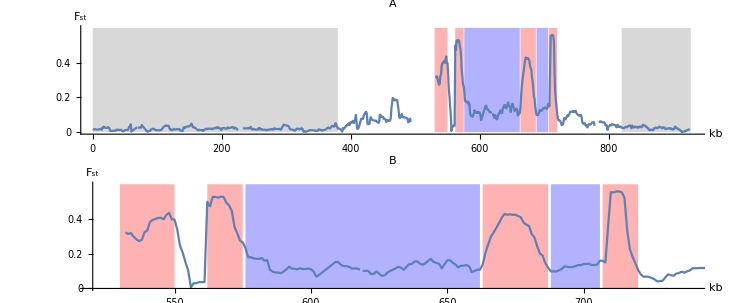

```mathematica
pf=plotFst[{4,5},{Δ,δ,ct,Δs,pools,θ},PlotRange->{{0,930000},{0,0.6}}];
shading=MapThread[Graphics[{Opacity[0.3],#2,Rectangle[{#1⟦1⟧,0},{#1⟦2⟧,0.6}]}]&,{window2/@{"left of ROS","ROS1 A","ROS1 B","between Ros/EL A","third peak","between Ros/EL B","EL","right of EL"},{Gray,Red,Red,Blue,Red,Blue,Red,Gray}}];
bs={FontFamily->"Times",FontSize->14};al={"kb","F_st"};
tks1={{{0,"0"},{200000,"200"},{400000,"400"},{600000,"600"},{800000,"800"}},{0,0.2,0.4}};
tks2={{{550000,"550"},{600000,"600"},{650000,"650"},{700000,"700"}},{0,0.2,0.4}};
Show[GraphicsColumn[{
Show[shading,pf,PlotLabel->"A", AspectRatio->0.2,PlotRange->{{0,930000},{0,0.6}},BaseStyle->bs,Axes->True,AxesLabel->al,Ticks->tks1],
Show[shading,pf,PlotLabel->"B",AspectRatio->0.2,AxesOrigin->{520000,0},PlotRange->{{520000,740000},{0,0.6}},BaseStyle->bs,Axes->True,AxesLabel->al,Ticks->tks2]}]]
```

Figure S9. Plot of F_st across the 930kb ROS/EL scaffold (A), and in the 220kb region covering the ROS/EL region (B), for pools YP1, MP2, which are 2.5 Km apart. Shading indicates the regions used to make parameter estimates. Grey: flanking regions, outside the influence of ROS/EL; pink: peaks in F_st at ROS1, middle, and at EL; blue: non-peak regions in-between ROS and EL.

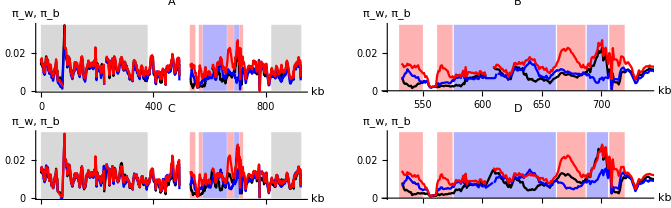

```mathematica
pw[k_,c_]:=pw[k,c]=plotPiWithin[k,{Δ,δ,ct,Δs,pools,θ},PlotStyle->c,Joined->True,PlotRange->{{0,930000},{0,0.035}}];
pb[{j_,k_},c_]:=pb[{j,k},c]=plotPiBetween[{j,k},{Δ,δ,ct,Δs,pools,θ},PlotStyle->c,Joined->True,PlotRange->{{0,930000},{0,0.035}}];
shading=MapThread[Graphics[{Opacity[0.3],#2,Rectangle[{#1⟦1⟧,0},{#1⟦2⟧,0.035}]}]&,{window2/@{"left of ROS","ROS1 A","ROS1 B","between Ros/EL A","third peak","between Ros/EL B","EL","right of EL"},{Gray,Red,Red,Blue,Red,Blue,Red,Gray}}];
bs={FontFamily->"Times",FontSize->14};al={"kb","π_w, π_b"};
tks1={{{0,"0"},{200000,"200"},{400000,"400"},{600000,"600"},{800000,"800"}},{0,0.01,0.02,0.03}};
tks2={{{550000,"550"},{600000,"600"},{650000,"650"},{700000,"700"}},{0,0.01,0.02,0.03}};
Show[GraphicsGrid[MapThread[{Show[shading,pw[#1⟦1⟧,Black],pw[#1⟦2⟧,Blue],pb[#1,Red],AspectRatio->0.2,Axes->True,PlotRange->{{0,930000},{0,0.035}},BaseStyle->bs,Axes->True,AxesLabel->al,Ticks->tks1,PlotLabel->#2,ImageSize->Full],Show[shading,pw[#⟦1⟧,Black],pw[#⟦2⟧,Blue],pb[#,Red],AspectRatio->0.2,BaseStyle->bs,Axes->True,AxesOrigin->{520000,0},AxesLabel->al,Ticks->tks2,PlotRange->{{520000,740000},{0,0.035}},PlotLabel->#3,ImageSize->Full]}&,
{{{1,8},{4,5}},{"A","C"},{"B","D"}}]]]
```

Fig. S10. Plots of diversity, π_w, within striatum (black lines) and pseudomajus (blue lines), and divergence between them (π_b, red lines). This shows two pairs of pools (A, B: YP4, MP11, ~20Km apart; C, D: YP1, MP2, 2.5Km apart). A, C)  the whole 930kb region; B, D) the 220kb region between ROS and EL. Shading indicates regions, as in Fig. S9. Peaks in F_st at ROS and EL appear to be due to reductions in diversity on both sides, whereas the middle peak appears to be due to increased divergence. There are also regions where there is reduced diversity on one side, but where π_w is close to π_b on the other side (e.g. right of ROS, left of the middle peak, and left of EL); such an asymmetric loss of diversity does not increase F_st enough to give an obvious peak.

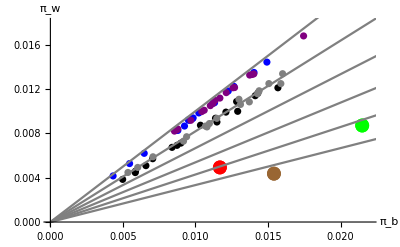

```mathematica
Show[MapThread[ListPlot[piReps[s[#1],1,40,4,17,100]⟦1⟧,PlotStyle->#2]&,{{0,6.4},{Black,Blue}}],MapThread[ListPlot[piReps[s[#1],2,40,4,17,100]⟦1⟧,PlotStyle->#2]&,{{0,6.4},{Gray,Purple}}],
plotPi[{4,5},5;;-5;;10,{Δ,δ,ct,Δs,pools,θ},0.03,{"peak 1","peak 3","peak 4"},{Red,Green,Brown},{0.025,0.025,0.025}],AxesLabel->{"π_b","π_w"},PlotRange->{{0,0.022},{0,0.018}},AxesOrigin->{0,0},BaseStyle->{FontFamily->"Times",FontSize->14}]
```

Fig. S11  Mean diversity within populations, π_w, plotted against divergence, π_b, for simulations, at T=0.4 N_e generations. Results are from 4 simulations: two replicates with N_e m=3.2 (blue/purple) and two with no gene flow (black/grey). For each simulation, the genome is assigned to 19 windows, each representing 10kb.  The large dots show the three F_st peaks, at ROS, EL and in-between (red, brown, green), as in Fig. 3.

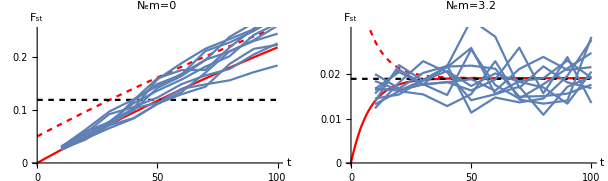

```mathematica
grpp[m_,fm_,tks_,fo_]:=Show[Plot[{Fst[t/200,m,2],Fst[t/200,m,2,0.05],fo},{t,0,100},PlotRange->{{0,100},{0,fm}},PlotStyle->{Red,{Red,Dashing[{0.01,0.01}]},{Black,Dashing[{0.01,0.01}]}}],Table[ListLinePlot[tabFst[m,k]],{k,10}],
PlotLabel->("M="<>ToString[m]),BaseStyle->{FontFamily->"Times",FontSize->14},Ticks->{{0,50,100},tks},AxesLabel->{"t","F_st"}];Show[GraphicsRow[MapThread[grpp,{{0,6.4},{0.25,0.03},{{0,0.1,0.2},{0,0.01,0.02}},{Mean[fstObs[RosElWindowsNO]],Mean[fstObs[refWindowsNO]]}}]]]
```

Fig. S12  Increase in F_st over time for 10 replicate simulations, with N_e m=0 or 3.2 (left, right). Each line is the average of 100 replicate throws of the SNP onto the simulated ancestries.  The horizontal dotted line shows the observed F_st=0.12 in-between ROS and EL (left), and F_st=0.019 outside ROS/EL (right).  Red lines show the theoretical prediction, based on expected coalescence times (S5.1).  The lower red line shows how F_st increases, when starting from zero in primary contact, whilst the upper dashed red line shows the expected change, starting from F_st=0.05, following secondary contact.  This figure extends Fig. 6, by showing how F_st changes through time, in multiple replicates.

```mathematica
(wn=window[#];tt=Select[tabulatePi[{4,5},{Δ,δ,ct,Δs,pools,θ}],wn⟦1⟧<#⟦1⟧≤wn⟦2⟧&];tt⟦5;;-5;;10,{2,3,4}⟧/.{π1_,π2_,πb_}:>(πb-(π1+π2)/2)/(πb+(π1+π2)/2))&/@{"peak 1","peak 3","peak 4"}
```

{{0.407011},{0.423403},{0.558616}}

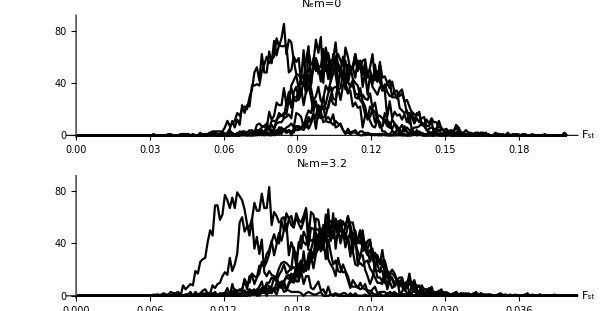

```mathematica
del0=0.001; del6=0.0002;
fn[{πb_,πw_}]:=(πb-πw)/(πb+πw);
grr[m_,fm_,δ_]:=Show[Table[ListPlot[Transpose[{Range[δ/2,0.2-δ/2,δ], BinCounts[Flatten[Map[fn,piReps[s[m],k,40,4,17,100],{2}]],{0,0.2,δ}]}],Joined->True,PlotLabel->"N_em="<>ToString[m/2],PlotRange->{{0,fm},{0,90}},Ticks->{Automatic,None},PlotStyle->Black,AxesLabel->{"F_st",None},AspectRatio->0.25,BaseStyle->{FontSize->14,FontFamily->"Times"}],{k,10}]];Show[GraphicsColumn[MapThread[grr,{{0,6.4},{0.2,0.04},{del0,del6}}]]]
```

Fig. S13. The distribution of F_st without gene flow (top) and with gene flow (N_e m =3.2; bottom), for 10 replicate simulations, at t=0.4 N_e. Each distribution represents variation in F_st due to 100 random draws of the SNP, conditional on the ancestry of each of the 10 replicates.  For N_e m = 3.2, the standard deviation of F_st between replicates, due to random ancestry, is 0.0031, and within replicates, due to random SNP, is 0.0027; for N_e m=0, the s.d. are 0.0129, 0.0133 respectively.

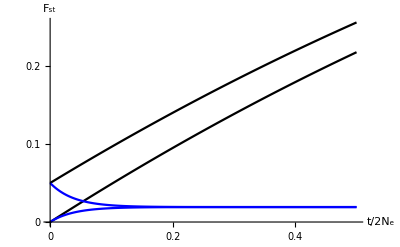

```mathematica
Plot[{Fst[T,0,2],Fst[T,6.4,2],Fst[T,0,2,0.05],Fst[T,6.4,2,0.05]},{T,0,0.5},PlotStyle->{Black,Blue},AxesLabel->{"t/2N_e","F_st"},BaseStyle->{FontFamily->"Times",FontSize->14},Ticks->{{0,0.2,0.4},{0,0.1,0.2}}]
```

Fig. S14 The change in F_st over time, for ancestral population size θ=2, and M=0,6.4 (black, blue). The initial F_st is 0 or 0.05.  WIthout migration, F_st initially increases linearly at a rate T/2, whilst with migration, it rapidly approaches 1/(1+8M).

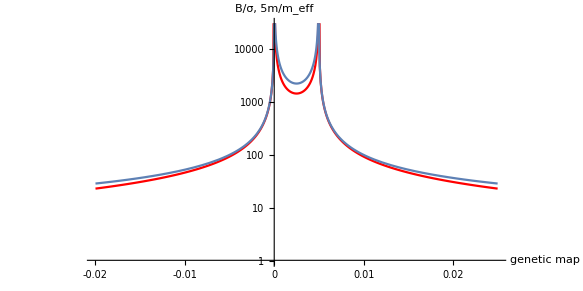

```mathematica
pln=pSol[0.5,0.005,0.05,0,20,100];
δ=0.0001;ϵ=10^-5;pr={{-0.02,0.025},{1,3 10^4}};
tt=Table[{r,If[Abs[r]<10^-5∨Abs[r-0.005]<10^-5,10^6,barrier2[r,0.5,0.005,pln⟦-1⟧]]/√0.5},{r,-0.02,0.025,δ}];
Show[ListLogPlot[tt,PlotRange->pr,Joined->True,BaseStyle->{FontFamily->"Times",FontSize->12},AxesLabel->{"genetic\nmap","B/σ, 5m/m_eff"},Ticks->{{-0.02, -0.01,0,0.01,0.02},{10,100,1000,10^4}},AspectRatio->0.5,PlotStyle->Red],
Show[LogPlot[5/Meff[r,0.005,0.05],{r,-0.02,0.025},PlotRange->pr]]]
```

Figure S15. Strengths of the barrier to gene flow between two demes (blue) and in one dimension (red), plotted across the genetic map.  There are two selected loci, each with divergence maintained by selection of strength s=0.05, and at positions 0, 0.005 on the genetic map (i.e., 0.5cM apart). The barrier to flow between two demes is represented as 5m/m_eff, a scaling which makes the barriers comparable in strength.

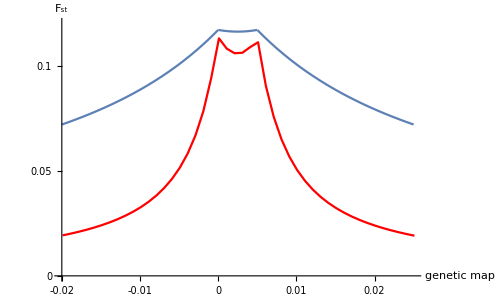

```mathematica
Show[Plot[Fst[0.25,6.4Meff[r,0.005,0.05],2],{r,-0.02,0.025},PlotRange->{{-0.02,0.025},{0,0.12}}],ListLinePlot[tbl[20,300.,{100,101},0.02],PlotStyle->Red],AxesLabel->{"genetic\nmap","F_st"},BaseStyle->{FontFamily->"Times",FontSize->14},Ticks->{{-0.02,-0.01,0,0.01,0.02},{0,0.05,0.10}},AxesOrigin->{-0.02,0}]
```

Figure S16  Comparison between the effects of a barrier on F_st between two demes (blue), and immediately on either side of a barrier in one dimension (red). Two loci, each under selection s=0.05, and r=0.5cM apart, are assumed. For one dimension, values are for 200 demes, each of 150 diploid individuals, with a reduction in gene flow between demes 100, 101; results are shown at 2000 generations.  For flow between two demes (blue), N_e m=6.4, and T=0.5 N_e. Here, F_st is calculated by comparing the probability of coalescence more recently than 2000 generations, between two genes on different sides of the barrier, P_b, with that between two genes from within the same location, P_w.  Assuming that lineages that do not coalesce in this recent interval share ancestry much further back, F_st=(P_w-P_b)/(P_w+P_b).  The probability of coalescence before time t between genes in demes i, j, P_(t,i,j), is calculated from the recursion P-t+1 = ℐ/(2N) + (1 - ℐ/(2N)) M.P_t.M^T, where ℐ is the identity matrix, and M the migration matrix, which includes the effects of the barrier. The code is given in the accompanying Mathematica notebook.

#### Working

```mathematica
fn[k_,s1_,s2_]:={Prepend[StringPartition[s1,3],k],Prepend[((" "~~#~~" ")&/@Characters[StringDelete[s2," "]])," "]};
```

```mathematica
TableForm[MapThread[fn,{{"  1"," 61","121","181","241","301","361","421","481","541","601"},
{"ATGAAAAAAAGATCTTGCAGTACTGAAGGGAAGTATACAAAAGGGGCTTGGTCACTGCAA","GAAGATCAAAAGTTGATTGATTGTGTAAACACTCATGGTGAAGGATGTTGGCGTACCATC","GCCCAAGCTGCTGGGCTGCATCGTAGCGGGAAAAGTTGCATGTTGAGATGGAAAAACTAC","CTAAAGCCCGTCACCAGCTTTGGGGAAGACGAAGAGGACCTCATAATCAGGCTCCATGCA","CTCCTTGGCAACCGGTGGTCTCTAATTGCGGGACGTTTGCCGGGGCGAATGGATGATGAA","GTGAAGAACCATTGGAATTCACATCTAAAGAGAAAGCTGATAAACATGGGCGTCGATCCA","AATAACCACTGTGTGAACGAAACTCTACAGCCTACCAACGTTTGTTCTGAAGATGATGAT","GATATTACAACATTGTCTGTCTCAAAATCCAAAAGAACTCGTTCGGACAATCATTCCTCG","GAATCGATTAGTTCCCCTGTTGATCCTGAAGAAGCCCTAAGCAACACCTGCGACTTAACG","GCTTCGGCAAAGAAGCAGGATTTAAGCGCAAATCATGTTAAAGATGAAAATGATGAGGCG","ATGAATTAG"},
{"M   K K R S C S T E G K Y T K G A W S L Q","E D Q K L I D C V N T H G E G C W R T I","A Q A A G L H R S G K S C M L R W K N Y","L K P V T S F G E D E E D L I I R L H A","L L G N R W S L I A G R L P G R M D D E","V K N H W N S H L K R K L I N M G V D P","N N H C V N E T L Q P T N V C S E D D D","D I T T L S V S K S K R T R S D N H S S","E S I S S P V D P E E A L S N T C D L T","A S A K K Q D L S A N H V K D E N D E A","MN*"}}],TableAlignments->Left,TableSpacing->{1,0}]
```

## Supplementary Tables

Table S1 Population sampling.

Taxon | Location | Population
code | Latitude | Longitude | Number of
individuals
A.m.striatum | Planoles | YP4 | 42.359921 | 1.926958 | 52
A.m.striatum | Planoles | YP2 | 42.32584 | 2.054797 | 50
A.m.striatum | Planoles | YP1 | 42.326943 | 2.052929 | 50
A.m.pseudomajus | Planoles | MP2 | 42.323325 | 2.082989 | 50
A.m.pseudomajus | Planoles | MP4 | 42.322234  | 2.091375 | 50
A.m.pseudomajus | Planoles | MP11 | 42.331038  | 2.170284 | 50
A.m.striatum | Mont Louis | ML | 42.507672  | 2.123323 | 58
A.m.striatum | Camurac | CAM | 42.800751  | 1.927576 | 50
A.m.pseudomajus | Cintegabel | CIN | 43.311569   | 1.533579 | 42
A.m.pseudomajus | Chioula | CHI | 42.775920  | 1.866869 | 49

Table S2 Sequencing overview for PoolSeq

Population
code | Sequencing
center | Number of
read pairs | Read length (bp) | Index | Number of read
pairs retained for
mapping after QC | Proportion of
reads retained for
mapping
YP4 | BGI | 451955888 | 100 | ATCACG | 373327071 | 0.83
YP2 | Earlham Institute | 125241587 | 101 | ACAGTG | 107958012 | 0.86
YP1 | Earlham Institute | 154987202 | 101 | CTTGTA | 134707676 | 0.87
MP2 | Earlham Institute | 163039507 | 101 | GCCAAT | 143021119 | 0.88
MP4 | Earlham Institute | 153285000 | 101 | ACAGTG | 135677864 | 0.89
MP11 | BGI | 411774991 | 100 | GCCAAT | 290092843 | 0.70
CIN | BGI | 251478965 | 150 | GACCA | 237047926 | 0.94
ML | BGI | 236963411 | 150 | CAGTG | 223896625 | 0.94
CAM | BGI | 280146409 | 150 | TCCGC | 264611490 | 0.94
CHI | BGI | 280394487 | 150 | TGAAA | 265294220 | 0.95

Table S3 Mapping overview for PoolSeq

Pop'n
code | Library
insert size | Mean
variant
frequency | Library
duplic'n
prop'n | Number of
reads after
processing | Proportion
of reads
mapped | Proportion of
mapped reads
properly paired | Mean
coverage | Median
coverage | Prop'n 
genome 
cov. >10x
YP4 | 249.±40.2 | 0.0283 | 0.32 | 541229067 | 0.8 | 0.8 | 44.3 | 33 | 0.72
YP2 | 516.7±57.9 | 0.0242 | 0.19 | 176336299 | 0.95 | 0.95 | 19.4 | 20 | 0.72
YP1 | 365.4±34.7 | 0.0249 | 0.37 | 175705301 | 0.92 | 0.92 | 18.5 | 19 | 0.71
MP2 | 320.4±24.8 | 0.0245 | 0.41 | 174386564 | 0.93 | 0.93 | 18.5 | 19 | 0.71
MP4 | 490.1±45.9 | 0.0247 | 0.28 | 199515082 | 0.94 | 0.94 | 21.0 | 22 | 0.73
MP11 | 272.4±28.3 | 0.0271 | 0.37 | 384498107 | 0.88 | 0.88 | 31.4 | 23 | 0.61
CIN | 545.5±119.8 | 0.0242 | 0.15 | 406993391 | 0.94 | 0.94 | 73.4 | 85 | 0.81
ML | 538.8±120.5 | 0.0268 | 0.24 | 343333174 | 0.96 | 0.96 | 55.8 | 64 | 0.79
CAM | 542.8±123. | 0.0246 | 0.16 | 451190592 | 0.94 | 0.94 | 79.8 | 93 | 0.82
CHI | 541.5±121.7 | 0.0242 | 0.15 | 451975369 | 0.96 | 0.96 | 81.9 | 95 | 0.82

Table S4 Primers for polymorphic markers used for genotyping natural and mapping populations. The primers are ordered by their location on chromosome 6. In cases where the marker targets a particular SNP, its position is indicated. Markers in the genes ROS1, ROS2, ROS3 and EL-MYB are indicated.

Marker
number | Genotyping
method | Primer
orientation | 5’ primer
position | Focal
SNP | Gene | Sequence (5’-3’)
1 | MULTIPLEX | F | 316853 |   |   | TTGGCCCAACTAAGATGATAAG
  |   | R | 317232 |   |   | CTTACGAAACAAATCGGCTCAT
2 | MULTIPLEX | F | 342846 |   |   | TTGGTGGGCCTAACTTTTCTTA
  |   | R | 343237 |   |   | TCAACAATTCTCACCCCCTGTT
3 | MULTIPLEX | F | 466813 |   |   | TTCTCGTCACTTTACAACACTGAAC
  |   | R | 467222 |   |   | GAAACATGGGGACTTCAACAAT
4 | KASP | F | 528885   | 528910 |   | AGGTTTCTGAAGCGCCAGGTTC
  |   | R | 528931  |   |   | AATGCGACAACAACGTCTAACG
  |   | R | 528931  |   |   | AATGCGACAACAACGTCTAACA
5 | PCR | F | 541186   |   | ROS1 | GGCTCCACCCTATGATGTATGT
  |   | R | 541644   |   | promoter | GAGTACCCCTTGAGCGAAACTT
6 | KASP | F | 541834    | 542000 | ROS1 | TGGCATCAAGTTCCACACAGAGCAG
  |   | R | 542020   |   | intron1 | CAACATTGACGTACGGTATTC
  |   | R | 542020  |   |   | CAACATTGACGTACGGTATTT
7 | MULTIPLEX | F | 543023   |   | ROS1 | ACTATCCGAGTTGAACAATCTGGCCA
  |   | R | 543395   |   | intron2 | AGTTTCAACAAGACGGGAGCTA
8 | CAPS | F | 542992    | 543323 | ROS1 | CAATGTGCATGTCCTTCCTAAA
  |   | R | 543503   |   | intron2 | ATGGACCCCGCTAAACACTTA
9 | SANGER | F | 543581   |   | ROS1 | TGTCCGGTAAGAAAGAAAAGGA
  |   | R | 544170   |   | exon3 | TCTCATTGTCTAACGGTTGCA
10 | SANGER | F | 566650   |   | ROS2 | GCCTAAATCCTTAGGAAATTGC
  |   | R | 567213   |   | exon3 | GGCTTAAACAATCCGTTGTGA
11 | CAPS | F | 566775    | 566852 | ROS2 | TTGGAATACTCATGTGGGGAAG
  |   | R | 567136   |   | exon3 | ATTCAGACATTTTTCCGGTTTG
12 | KASP | F | 566979    | 567004 | ROS2 | AGATTATGAGAAGCAAAAG
  |   | R | 567023   |   | exon3 | GTTGAGGCCACATTATTGTG
  |   | R | 567023  |   |   | GTTGAGGCCACATTATTGTA
13 | KASP | F | 575590    | 575623 | ROS3 | GGATGGATTATCAAAATTCTAC
  |   | R | 575644   |   | intron2 | CTACAAAAGATTATGTCCTACT
  |   | R | 575644  |   |   | CTACAAAAGATTATGTCCTACA
14 | PCR | F | 616606  |   |   | GGAGAGGAAGGGGTTGTTGG
  |   | R | 618300  |   |   | AGAGTTGTGGGATTGGAGTAA
15 | SANGER | F | 626228   |   |   | AAATTAAACTAAAAACGCGAGGAT
  |   | R | 626401  |   |   | TCAATATCTTTCCTACTCACGTCCT
16 | MULTIPLEX | F | 637333  |   |   | ACGTCGAATTTGTTGAAGACCT
  |   | R | 637553  |   |   | TGCAACATAACTAAATTCCCACTC
17 | SANGER | F | 650759  |   |   | AGAAGTTTGTACCCGGAAATGA
  |   | R | 651324  |   |   | GTTTTGGCTTTCTTTGAAGCAC
18 | SANGER | F | 651551  |   |   | AGGATCTTGTCCCGAATGGT
  |   | R | 652136  |   |   | AGTAGCCAAAACCTGCACAAAT
19 | KASP | F | 652993   | 653015 |   | AAATTAAGCTGTACATTAATTAC
  |   | F | 652993  |   |   | AAATTAAGCTGTACATTAATTAT
  |   | R | 653040  |   |   | TTCAGCAGTTTAAGGGAG
20 | PCR | F | 653629  |   |   | CCCTGTGACCTTGTCTTCTTTT
  |   | R | 654198  |   |   | GAAGTCCTTTGTTTTGCTGAGA
21 | SANGER | F | 654805   | 655252 |   | CTGGTGTTCAAGGAGTTGGTT
  |   | R | 655699  |   |   | AGCAAGCAGTATCGCATCATT
22 | SANGER | F | 667783   | 668233 |   | CATCAAAGTGGGGAAGAAGGT
  |   | R | 668683  |   |   | TAAGAAAAATGGGGCAAACAG
23 | SANGER | F | 674804   | 675235 |   | TCTGTGTGCAGGCAAGAAACT
  |   | R | 675666  |   |   | GCAGCAGTAAGAAGGAACCAA
24 | SANGER | F | 678075   | 678655 |   | TAACAAGGGCCAAAAAGAGGT
  |   | R | 679234  |   |   | GGTGCCAACAACTTAAAACGA
25 | SANGER | F | 680007   | 680529 |   | AATCGTATCTGGTGCTGATGG
  |   | R | 681051  |   |   | CGCTGATCCAAGCTGATAAAG
26 | RNAseq | - | - | 688352 |   | -
27 | RNAseq | - | - | 688550 |   | -
28 | RNAseq | - | - | 688746 |   | -
29 | SANGER | F | 699584  |   |   | ATTCAGATCCAAGCATGAAAGC
  |   | R | 700542  |   |   | GTGCATCACAACTCACAATGAA

Marker
number | Genotyping
method | Primer
orientation | 5’ primer
position | Focal
SNP | Gene | Sequence (5’-3’)
30 | PCR | F | 712107   |   | EL-MYB | AAACGTGAAGTAATTCTAGCTGCA
  |   | R | 715005   |   | exon3 | CGAATGGATGATGAAGTGAAGA
31 | PCR | F | 713692   |   | EL-MYB | AAACTCGATCCACCTTGGTATT
  |   | R | 715005   |   | exon3 to 
3’ UTR | CGAATGGATGATGAAGTGAAGA
32 | MULTIPLEX | F | 715097   |   | EL-MYB | ATGAAGAAAAAGCTTAGGTGAACT
  |   | R | 715266   |   | intron2 | GGGATGGTGTGCTACCTTTT
33 | KASP | F | 716969    | 717045 | EL-MYB | CATTGTCATGACTCGTTCAACA
  |   | R | 717066   |   | promoter | GAATATATTTAAAGTGAGAGTA
  |   | R | 717066  |   |   | GAATATATTTGAAGTGAGAGTC
34 | PCR | F | 716969    |   | EL-MYB | CATTGTCATGACTCGTTCAACA
  |   | R | 717779   |   | promoter | TTAAACTGAAAGGCAGGCAATC
35 | SANGER | F | 735046  |   |   | CAGACGTTTTAGGTTCCACCA
  |   | R | 736154  |   |   | GGTGTTCATCCACATTGCTCT
36 | SANGER | F | 774993  |   |   | ACTCGGAAGATGAGGGAAAAA
  |   | R | 776141  |   |   | ATCAAGTCGTTGTCGTCGTTC
37 | PCR | F | 857452  |   |   | AGTCCCCGAAATGTAAGTTGTG
  |   | R | 858371  |   |   | CCGAGTCTTTCTAGCCACGTAT
38 | MULTIPLEX | F | 864557  |   |   | CAGATTGGTTCTTACACCGTCA
  |   | R | 864794  |   |   | GAAGTGGAATTTTGTGGAGGAG
39 | SANGER | F | 864282  |   |   | GTTCGGTTTCTCGAATGGATAC
  |   | R | 865281  |   |   | AGATGACAAAGGTGGCAAATCT

Table S5 Sequence for KASP oligos for SNP loci used in geographic cline analyses. Focal SNP indicated with square brackets (e.g. [A/G]) with remaining sequence in IUPAC code. For each SNP,* = within ROS1, **= ROS2, ***= ROS3, ^= EL

SNP | Position (bp) |  
1   | 18402 | TCCTCTGGAAAAACCATGGTTGCGYTCAATTTGTTTATCACCAAAGATGC[A/G]GCA
CATTCCATTCCTAYGTAGCCTCCRCCAATAACTACGGCATTTCCRCC
2   | 30843 | CCAAAAGTAGTCATTTGATTCAGTAGGGAAGTGATTAGGATATTGAACGT[C/T]ATT
TYCCATATTGCCATTGAAAGAAKAAGAGTAAGATTCAACTGCATGAT
3   | 108441 | CTTTTMGAAAATTGAACAAAAGCCCGCTCACCATGGGCAGGAATATAAAT[A/G]TT
AATAACTTGACCAAATCTTTGAAAATGWGARAGAAGRGATTCCCTTCT
4   | 181917 | CGAYTGGCCCAAGTTTAAAACTTTTGCTTACGTGGCGAAATAATAAGCAA[C/T]GA
GGGCAAGTGACTGGCTAATAAAAGGCCCAAATCCCAAAATTGTYWCAT
5   | 473914 | AGAAAGCATCAGCCGATAAAACCTCAGCCCACTGCAAGTTTTGAYAGCCA[A/G]YG
AAGTTAAGAGGGAARYAAACAGMGACCGAAATTGATGCTCGGTATGGA
6  | 490488 | TTGGCTGGCAGACCCAAAKTTCATCACATGGTTCTCTTACAMCGATGTAC[G/T]WT
GCTGTCCGTCAATCAATTCTTGTTAATTGAAAAAATATAATTACSAAT
7^* | 541834 | TGGCATCAAGTTCCACACAGAGCAG[G/A]AATACCGTACGTCAATGTTG
8^*  | 543443 | ARTAGTGAAAACTAT[A/G]CWTCAATTAGTTAT
9   | 544601 | AYTAGTGATCTTTTA[C/T]TTGAGGGTAGCAAC
10^(**) | 567004 | CGGATAACTAGTACCACTGAAAATCTAGATTATGAGAAGCAAAAGCCGTTT[C/T]A
CAATAATGTGGCCTCAACACCAGAAGAAGTCGATGAAAGCATTAGATGGTG
11^(***)  | 575837 | TTTGTACATCCATTGTATTTCTCCATCAATTTTTTCATCTATATAKTGYT[C/G]AAGC
AGATGGACGCTGATTGCCGGTAGACTTCCTGAAAGGACAGCGAACG
12^(***)  | 576271 | GTGTTTTCTCCATCGAYGACCTTCATRTTTGGGACGTGGTAGACATGGAC[G/T]ATC
AATGATTCGTGTCTATTACTTAATTTGTTCGCGTTTGAGKTGTCTTT
13  | 618376 | CAAACTGGAAATATAGTCACGAGTTCATTCATGCTATACTTGAAGAAWCC[A/G]TA
GAACTTATCAACTGAAGCATGTATTGCAGTGCTCACTTCGTATTTCTC
14   | 620992 | ATGTATTTCTGTTGTAAACACGTGATCCAWGACATGCACCTACAACAATT[A/T]GTT
TGGTAGAARTAAAAGCGAGGTKACCTKTAGGATAGAAAAAGAAAACA
15   | 635819 | CTKAATTATAAGCACTCACTTTTTYATAATTCTATTCCAATCCYTCATTA[A/T]GATA
AATAAACGAATAGTACACAATTCATRRATCAAAATTTCGATTTCGA
16   | 653015 | CAAYTTTWWWTCGCTGATTCTCAATAAATTAAGCTGTACATTAATTA[C/T]GCACT
TTCTCCCTTAAACTGCTGAARYAAATAAAAWTCACGTTGCTGAAAGAT
17   | 670530 | ATCGACTGGCAAGGTAGAGCGGTTGCCTTGAATGCTGGTAGCAAAACATC[C/G]AG
TGCATCTGCATTTTTCTTACCATTAGAACGGGTAAATAGATGTAGTCT
18  | 674756 |  
19   | 689955 | ATATTARTTARTTGTATATGGGTGAACTATCAATGACATTTATTGGCCYT[C/T]GTT
WAATAATAGGAGAARTAYTCAATTCTCATGCTTTGGAAATCACGAAA
20 | 702909 | TCTGATTCWAGAAGAACATATAYATGTGATCGKATAATCTTTAAGCACGT[C/T]GA
TTGCTTTCAACGACAACTTYATTTGAAGAATTTGGCGYCRTTTTTCAT
21^^  | 715001 | TCARCTTTCTCTTTAGAYGTGAATTCCAATGGYTCTTCACTTCATCATCC[A/G]TTCG
SCCCGGYAARCGTCCCGCAATTAGAGACCACCTAACAGTMAAGAAA
22^^  | 715015 | AGAYGTGAATTCCAATGGYTCTTCACTTCATCATCCRTTCGSCCCGGYAA[A/G]CGT
CCCGCAATTAGAGACCACCTAACAGTMAAGAAAGTGAATTAATAYAA
23   | 717957 | TTTAATTTCCATGCAATAGTCATGAGACCCACATTTTGCTCATGACATGT[A/C]TAGT
GASAATAAATTACRTAATTAAAAATAATGAATRTACACGAACTTTG

SNP | Position (bp) |  
24   | 737420 | GATTTATTATTGGAGAAAGGCCACAATTATTGCTTCTGTTYCCTGATTCT[A/G]TTTC
TATCTACTTGCMATTTGCATGAAATCWTGGCTTCAAGTTCTTCTCT
25   | 744403 | GACACYACAAAATTATTCCGAGTAAAGAACGATAGAATCTCCCCYGCCAC[C/T]CG
ATTAGGCGCCGTCTTCATCTCTCCTTCTCCTACAAAAGTTTTCTTCAC
26   | 748981 | AAACAACCGGWGGGGCRGGAGGCCYGGTCAATAATCCTTGAATCAAAGGG[A/C]A
AATGTTGCAGGATCCTTCATCTCCATAAAAACAAACACTCTCCATTGAA
27   | 758578 | TGTCCATTTTACCCTYGYTATCCCATTARAAGATATTTCAAAAAAGTGTA[A/C]TCA
AAACATTATTGGATAAAATTTGCYGACACATTGACACCTAKATTTGG
28   | 849332 | AACCCATGAMTCAAATTGTTGTCTKTTGCTGGGTTGGCACGTATAWTCTG[C/T]GAA
TTAAGAATTACTRTWCCATAARAAAATGGACTGCCACTAGGCTTGAGAA
29   | 886245 | AGTATGCATAGGAGTCGGAATTACTTCTTCATTGGTCGAAGYTTGCAAGT[C/T]TTG
ATCMTCCCCAAAGCCCCARAGCTTTCTMAACCTATCCTTTTCAYKGG
30   | 887766 | ACATTCTAATTAATAASAACRGAYTATCTTTCTCAGAACCAACAAGGATA[G/T]GMC
AAACTRTCCCTCAGAATCRAAAGTGCCAGGACAAATCTAAAACTTGT

Table S6 Cline fit summary of KASP SNP loci across the ~900 Kbp region of chromosome 6 around ROS and EL. Best fit cline parameters for a symmetric sigmoid model for loci with strong allele frequency differences either side of the hybrid zone (>0.6). For SNPs,* = within ROS1, **= ROS2, ***= ROS3, ^= EL. Best fit parameters from maximum likelihood (logL) with 95% confidence interval in parentheses. Loci where no cline fitting was performed (<0.6) are indicated with a hyphen

SNP | Position (bp) | log(L) | center | width | p_0 | p_1
1  | 18402 | - | - | - | - | -
2  | 30843 | - | - | - | - | -
3  | 108441 | - | - | - | - | -
4  | 181917 | - | - | - | - | -
5  | 473914 | - | - | - | - | -
6  | 490488 | - | - | - | - | -
7^* | 542000 | -126.97 | 14.03 (13.9,14.2) | 0.97 (0.7,1.8) | 0.15 (0.09,0.21) | 0.98 (0.95,1)
8^*  | 543443 | -133.76 | 13.96 (13.8,14.1) | 1.48 (0.8,2.3) | 0.06 (0.04,0.13) |  0.99 (0.97,1)
9 | 544601 | -136.18 | 14.09 (14,14.2) | 1.28 (0.8,2)  | 0.08 (0.06,0.13) | 0.99 (0.97,0.99)
10^(**)   | 567004 | -135.42 | 14.01 (13.9,14.1) | 1.25 (0.8,1.9)  |  0.08 (0.03,0.13) | 0.98 (0.96,1)
11^(***)  | 575837 | -124.68 | 14.1 (14,14.2) | 0.88 (0.6,1.3) | 0.29 (0.23,0.33) | 0.99 (0.98,1)
12^(***) | 576271 | - | - | - | - | -
13 | 618376 | - | - | - | - | -
14 | 620992 | -136.74 | 14.14 (14,14.3) | 1.4 (0.9,2) | 0.36 (0.31,0.41) | 0.99 (0.98,1)
15 | 635819 | -143.89 | 13.77 (13.6,13.9) | 1.19 (0.8,1.7) | 0.25 (0.2,0.31) | 0.85 (0.81,0.88)
16 | 653015 | -151.03 | 13.97 (13.9,14.1) |  1.06 (0.7,1.6) | 0.17 (0.12,0.22) | 0.96 (0.93,0.98)
17 | 670530 | -140.73 | 14.03 (13.8,14.2) | 1.34 (0.7,2.3) | 0.31 (0.22,0.36) | 0.99 (0.98,1)
18 | 674756 | -175.92 | 13.99 (13.9,14.1) | 0.59 (0.5,0.9) | 0.26 (0.23,0.3) | 0.76 (0.73,0.8)
19 | 689955 | - | - | - | - | -
20 | 702909 | -167.07 | 13.97 (13.9,14.1) | 0.94 (0.6,1.5) | 0.34 (0.3,0.39) | 0.91 (0.88,0.93)
21^^ | 715001 | -165.78 | 14.01 (13.9,14.1) | 0.71 (0.5,1.1) |  0.11 (0.07,0.14) | 0.88 (0.84,0.9)
22^^ | 715015 | -165.06 | 13.99 (13.9,14.1) | 0.75 (0.5,1.1) | 0.11 (0.07,0.14) |  0.87 (0.84,0.9)
23 | 717957 | -125.08 | 14.16 (14,14.3) | 1.28 (0.8,1.7) | 0.07 (0.04,0.11) | 0.99 (0.97,1)
24 | 737420 | -176.06  | 13.97 (13.9,14.1) | 0.51 (0.5,0.9) | 0.48 (0.46,0.53) | 0.91 (0.9,0.93)
25 | 744403 | - | - | - | - | -
26 | 748981 | - | - | - | - | -
27 | 758578 | -177.2 | 13.07 (12.4,13.8) | 4.76 (2.7,7.5) | 0.23 (0.13,0.33) | 0.84 (0.8,0.88)
28 | 849332 | - | - | - | - | -
29 | 886245 | -165.51 | 11.7 (8.8,13.2) | 8.27 (4.7,18.9) | 0.42 (0.27,0.55) | 0.9 (0.86,0.96)
30  | 887766 | -179.3 |  11.2 (7.8,12.7)  | 11.05 (6.8,20) | 0.23 (0,0.34) | 0.88 (0.82,0.99)

Table S7 Statistics for two pairs of pools, for the regions defined in Fig. S9. This is based on overlapping 10kb windows, spaced at 1kb intervals. Windows are included if their left edge is within the boundaries of the region (col. 2). π_1, π_2 give the pairwise diversity within pools 4, 5 (striatum and pseudomajus), and π_b the pairwise divergence between them.  The last two columns show the mean and maximum F_st.  Values of π are weighted by the number of informative sites in each window, defined as having coverage between 15 and 500. The mean F_st is calculated from these weighted averages of π.

A) YP1, MP2 (2.5Km apart)

region | boundaries | kb | # windows | # sites | π_1 | π_2 | π_b | mean F_st | max F_st
left of ROS
right of EL | 0       380
820  927 | 487 | 466 | 2279945 | 0.01042 | 0.01015 | 0.01069 | 0.0192 | 0.0509
between ROS, EL | 576   662
688   706 | 104 | 101 | 420244 | 0.00881 | 0.00963 | 0.01186 | 0.1254 | 0.2333
ROS1 | 530   550
562   575 | 33 | 33 | 108623 | 0.00255 | 0.00653 | 0.01036 | 0.3911 | 0.5292
middle peak | 663   687 | 24 | 25 | 183534 | 0.01074 | 0.00641 | 0.01746 | 0.3413 | 0.4290
EL | 707   720 | 13 | 14 | 34500 | 0.00815 | 0.01055 | 0.01535 | 0.2429 | 0.5586

B) YP4, MP11 (~20Km apart) 

region | boundaries | kb | # windows | # sites | π_1 | π_2 | π_b | mean F_st | max F_st
left of ROS
right of EL | 0       380
820  927 | 487 | 466 | 2279945 | 0.01132 | 0.01041 | 0.01205 | 0.0516 | 0.2903
between ROS, EL | 576   662
688   706 | 104 | 101 | 420244 | 0.00840 | 0.00874 | 0.01295 | 0.2035 | 0.3305
ROS1 | 530   550
562   575 | 33 | 33 | 108623 | 0.00285 | 0.00599 | 0.01120 | 0.4339 | 0.6176
middle peak | 663   687 | 24 | 25 | 183534 | 0.00838 | 0.00970 | 0.01816 | 0.3351 | 0.4165
EL | 707   720 | 13 | 14 | 34500 | 0.00806 | 0.00967 | 0.01643 | 0.2990 | 0.5854

Table S8. The probability that the closest pair amongst k genes, thrown down on a linear map of length 5.88 Morgans, are closer than 0.5cM. See section S1.6.

k | P
5 | 0.0169
6 | 0.0252
7 | 0.0351
8 | 0.0465
9 | 0.0594
10 | 0.0737

Table S9. Summary population statistics for key population comparisons and genomic regions; based on windowed analysis (10kb windows, 1kb step size) of the 10 population dataset.

|   |   | F_st |   |   |   |   |  
  |   |   | YP1_MP2 | (2.5Km) | YP4_MP11 | (20Km) | CIN_ML | (100Km)
region | boundaries | # windows | median | mean | median | mean | median | mean
whole genome | all scaffolds>10kb | 455117 | 0.0357 | 0.0380 | 0.0543 | 0.0731 | 0.1193 | 0.1455
LG6 | all scaffolds>10kb 
mapped to LG6 | 43715 | 0.0358 | 0.0384 | 0.0421 | 0.0488 | 0.1917 | 0.2206
ROS chrom. arm | subset of LG6, 
 position >35Mb | 13331 | 0.0391 | 0.0436 | 0.0469 | 0.0557 | 0.2098 | 0.2340
ROS super-scaffold | ros_assembly 1-927kb | 810 | 0.0532 | 0.0975 | 0.0675 | 0.1143 | 0.2754 | 0.2904
ROS region (L peak) | ros_assembly 530-575kb | 43 | 0.3612 | 0.3369 | 0.3742 | 0.3477 | 0.5839 | 0.5196
EL region (R peak) | ros_assembly 707-720kb | 11 | 0.3411 | 0.3671 | 0.3692 | 0.3770 | 0.3439 | 0.3915
M peak | ros_assembly 663-687 kb | 25 | 0.3439 | 0.3236 | 0.3332 | 0.3138 | 0.1011 | 0.1166
interval between ROS, EL | ros_assembly 576-706kb | 125 | 0.1499 | 0.1849 | 0.2317 | 0.2286 | 0.3114 | 0.2889

| π_b |   |   |   |   |  
  | YP1_MP2 | (2.5Km) | YP4_MP11 | (20Km) | CIN_ML | (100Km)
region | median | mean | median | mean | median | mean
whole genome | 0.0082 | 0.0100 | 0.0101 | 0.0116 | 0.0093 | 0.0110
LG6 | 0.0071 | 0.0090 | 0.0079 | 0.0098 | 0.0080 | 0.0101
ROS chrom. arm | 0.0140 | 0.0145 | 0.0150 | 0.0154 | 0.0150 | 0.0156
ROS super-scaffold | 0.0161 | 0.0167 | 0.0173 | 0.0176 | 0.0166 | 0.0176
ROS region (L peak) | 0.0113 | 0.0109 | 0.0124 | 0.0114 | 0.0116 | 0.0105
EL region (R peak) | 0.0192 | 0.0202 | 0.0208 | 0.0214 | 0.0213 | 0.0209
M peak | 0.0250 | 0.0241 | 0.0259 | 0.0246 | 0.0198 | 0.0186
interval between ROS, EL | 0.0174 | 0.0192 | 0.0184 | 0.0197 | 0.0170 | 0.0196

| π_w |   |   |   |   |  
  | YP1_MP2 | (2.5Km) | YP4_MP11 | (20Km) | CIN_ML | (100Km)
region | median | mean | median | mean | median | mean
whole genome | 0.0077 | 0.0093 | 0.0085 | 0.0101 | 0.0069 | 0.0082
LG6 | 0.0066 | 0.0083 | 0.0072 | 0.0089 | 0.0050 | 0.0065
ROS chrom. arm | 0.0128 | 0.0133 | 0.0133 | 0.0138 | 0.0090 | 0.0097
ROS super-scaffold | 0.0136 | 0.0138 | 0.0142 | 0.0142 | 0.0094 | 0.0098
ROS region (L peak) | 0.0047 | 0.0049 | 0.0048 | 0.0050 | 0.0030 | 0.0029
EL region (R peak) | 0.0097 | 0.0101 | 0.0108 | 0.0100 | 0.0119 | 0.0096
M peak | 0.0118 | 0.0121 | 0.0126 | 0.0126 | 0.0152 | 0.0148
interval between ROS, EL | 0.0123 | 0.0130 | 0.0120 | 0.0120 | 0.0098 | 0.0108